Basic Structures: Sets, Functions, Sequences, Sums, and Matrices

## Introduction

Chapter 2 of the textbook covers mathematical objects fundamental to the study of discrete mathematics. We will see how the Wolfram Language represents these objects.

In Sections 1 and 2, we will see that the Wolfram Language’s implementation of a list can be used to model the mathematical concept of set. We will also see how to extend Mathematica’s capabilities to include fuzzy sets. In Section 3, we will consider different ways in which the concept of function can be represented in the Wolfram Language and how these approaches can be used in different circumstances. Section 4 will look at how to use lists to model finite sequences, how to represent recurrence relations, and how Mathematica can be used to compute both finite and symbolic summations. In Section 5, we will use Mathematica to list positive rational numbers in a way that demonstrates the fact that the rationals are enumerable. In Section 6, we will see how Mathematica can be used to study matrices.

## 2.1 Sets

Sets are fundamental to the description of almost all of the discrete objects that we will study. Mathematica provides support for both their representation and manipulation.

### Set Basics

In the Wolfram Language, sets are modeled as lists. Note that the syntax for a list matches the standard syntax for a mathematical set: a list of the elements of the set separated by commas and enclosed in braces. The elements can be any object. Typical examples are shown below.

```mathematica
{1,2,3}
```

{1,2,3}

```mathematica
{"a","b","c"}
```

{a,b,c}

```mathematica
{{1,2},{1,3},{2,3}}
```

{{1,2},{1,3},{2,3}}

```mathematica
{}
```

{}

In the first two examples above, the lists contain the numbers 1, 2, and 3, and the characters a, b, and c, respectively (note that the quotation marks distinguish them as strings and not symbols). In the third example, the elements of the list are themselves lists. The fourth example is the empty list.

Note, however, that Mathematica does not treat these list objects as sets, that is, it does not automatically respect the mathematical properties of sets. In particular, repetition and order make lists distinct, unlike mathematical sets. For example, consider the lists defined below.

```mathematica
set1={1,2,3,1,2}
```

{1,2,3,1,2}

Observe that when Mathematica echoes the list, it preserves the duplicate entries.

```mathematica
set2={2,3,1}
```

{2,3,1}

In addition, note that the order in which elements are entered is preserved.

To test whether two lists are the same, use the Equal (==) relation. Below, you see that Mathematica considers the lists set1 and set2 different from each other and different from {1,2,3}, despite the fact that, as sets, they are all identical.

```mathematica
set1==set2
```

False

```mathematica
set1=={1,2,3}
```

False

```mathematica
set2=={1,2,3}
```

False

In order to get Mathematica to recognize that set1 and set2 are equal as sets, you must force Mathematica to represent them in a canonical fashion. This is achieved with the Union function. We will see below how to use Union to find the union of two or more sets. When applied to a single list, Union returns the list obtained by sorting the elements and removing duplicates.

```mathematica
Union[{4,2,1,1,3,2,4}]
```

{1,2,3,4}

Because Union puts the elements of a list in a canonical order, the results of applying Union to two different lists that represent the same mathematical set will be the same.

```mathematica
Union[set1]==Union[set2]
```

True

It is a good idea, when doing work involving sets, to apply the Union function as part of the definition of the set.

#### Parts of Sets

Because the Wolfram Language uses lists to represent sets, you can use the Part operator to access individual elements and to select subsets based on their index. To obtain, for example, the fourth element, enclose 4 in double brackets.

```mathematica
set3=Union[{"a","b","c","d","e","f"}]
```

{a,b,c,d,e,f}

```mathematica
set3[[4]]
```

d

Negative values count from the right, so the second to last element (in the canonical order) is accessed as follows.

```mathematica
set3[[-2]]
```

e

By putting a list of indices within the double brackets, you can obtain any subset you wish. Note that the list must be contained in braces within the double brackets.

```mathematica
set3[[{1,3,4}]]
```

{a,c,d}

Finally, you can obtain a range of elements using the Span (;;) operator. For example, to obtain the second through fifth element, enter the following.

```mathematica
set3[[2;;5]]
```

{b,c,d,e}

#### Generating Sets

The Wolfram Language contains many functions that can be used to generate sets (lists). Two of these are Range and Table. Range is the simpler function and we describe it first.

The Range function is used to generate lists consisting of simple sequences of numbers. It has three basic forms. The first form of Range is with one argument. In this case, it produces the list of integers from 1 through the given value.

```mathematica
Range[8]
```

{1,2,3,4,5,6,7,8}

The second form of Range is with two arguments. In this case, it produces the list of values with the first argument as the starting value and the second argument as the maximum.

```mathematica
Range[-3,5]
```

{-3,-2,-1,0,1,2,3,4,5}

The third form takes three arguments. Again, the first argument is the starting value and the second is the maximum. The third argument specifies the “step,” that is, the difference between successive values in the list. For example, the following produces every third integer beginning with 2 up to 25.

```mathematica
Range[2,25,3]
```

{2,5,8,11,14,17,20,23}

Note that the maximum does not need to be a member of the list. Also note that the values given do not need to be integers. The command below produces the numbers beginning at 0.25 and increasing by 0.41 up until at most 7.

```mathematica
Range[0.25,7,0.41]
```

{0.25,0.66,1.07,1.48,1.89,2.3,2.71,3.12,3.53,3.94,4.35,4.76,5.17,5.58,5.99,6.4,6.81}

The second function, Table, gives you even more control over forming lists. Generally, Table requires two arguments. The first argument is an expression, often involving a symbol called the table index or table variable, that specifies the elements of the list being created. The second argument is a list defining the values that are to be substituted for the table variable in order to produce the list. There are five distinct forms for this second argument.

The simplest form of Table has no variable used in the first argument, and the second argument is a positive integer. This results in a list consisting of that many copies of the first argument. For example, to produce a list of seven fives, enter the following.

```mathematica
Table[5,7]
```

{5,5,5,5,5,5,5}

The other forms all use a table index. For these examples, we will use the variable i, and the expression that we give as the first argument will be i^2. This will produce lists whose elements are the squares of the values substituted for i. The second argument to Table, when using a variable, is always a list whose first element is the name of the variable, as in {var,...}.

If you evaluate Table with the second argument consisting of the variable and a positive integer, the result will be to substitute the integers 1 though the given integer for the variable. The following produces the squares of the integers 1 through 9.

```mathematica
Table[i^2,{i,9}]
```

{1,4,9,16,25,36,49,64,81}

In the next form, the second argument is the list consisting of the name of the variable and two numbers, a minimum and a maximum. The following produces the list of squares of the integers from 5 to 12.

```mathematica
Table[i^2,{i,5,12}]
```

{25,36,49,64,81,100,121,144}

You can also include a “step” by adding yet another number to the second argument. The following shows the squares of every other integer beginning at 4^2 and ending at 20^2.

```mathematica
Table[i^2,{i,4,20,2}]
```

{16,36,64,100,144,196,256,324,400}

In the final form of the second argument, you are able to specify an explicit list of values to substitute for the variable. You do this using the syntax {var,{values}}. That is, the second argument to Table is a list consisting of two elements: first the name of the variable, and second the list of values enclosed in braces. The following computes the squares of 2,3,5,7,11, and 13.

```mathematica
Table[i^2,{i,{2,3,5,7,11,13}}]
```

{4,9,25,49,121,169}

We summarize the allowed forms of the second argument to Table in the table below.

count | repeat count times
{i,i_max} | i ranges from 1 to i_max
{i,i_min,i_max} | i ranges from i_min to i_max
{i,i_min,i_max,step} | i ranges from i_min to i_max by step
{i,list} | i ranges over elements of list

Table can also be used with more than one variable in the expression. To do this, you simply provide an additional argument specifying each table variable. The Table function ensures that all combinations of values are included. For example, if f were a function of two values, the following would evaluate the function with the first value ranging from 3 to 9 and the second taking the values 0, 1, and 5.

```mathematica
tableExample=Table[f[i,j],{i,3,9},{j,{0,1,5}}]
```

{{f[3,0],f[3,1],f[3,5]},{f[4,0],f[4,1],f[4,5]},{f[5,0],f[5,1],f[5,5]},{f[6,0],f[6,1],f[6,5]},{f[7,0],f[7,1],f[7,5]},{f[8,0],f[8,1],f[8,5]},{f[9,0],f[9,1],f[9,5]}}

Note that this produces a nested list. If your goal is to produce a single list of all of the values, for example, to form the set {f(i,j)|3≤i≤9 and j∈{0,1,5}}, use Flatten to eliminate the nested structure and use Union to ensure that the result is canonically ordered and that duplicates have been removed. Be sure that Flatten is applied first.

```mathematica
Union[Flatten[tableExample]]
```

{f[3,0],f[3,1],f[3,5],f[4,0],f[4,1],f[4,5],f[5,0],f[5,1],f[5,5],f[6,0],f[6,1],f[6,5],f[7,0],f[7,1],f[7,5],f[8,0],f[8,1],f[8,5],f[9,0],f[9,1],f[9,5]}

#### Membership, Subset, and Size

The most basic question one can ask about a set is whether or not a particular object is or is not a member of it. In Mathematica, you do this with the MemberQ function. The first argument to MemberQ is the list and the second is the object being sought.

For example, if we use Table to define set4, the set of squares of integers from 0 to 10, we can use MemberQ to see that 4∈set4 but that 5∉set4. As mentioned earlier, when modeling a set as a list, it is a good idea to apply Union when defining it.

```mathematica
set4=Union[Table[i^2,{i,0,10}]]
```

{0,1,4,9,16,25,36,49,64,81,100}

```mathematica
MemberQ[set4,4]
```

True

```mathematica
MemberQ[set4,5]
```

False

The Length function returns the number of elements in a list.

```mathematica
Length[set4]
```

11

Be careful to keep in mind that if it is the cardinality of a set you are after, you must use Union or risk over-counting.

```mathematica
Length[{1,2,3,2,3}]
```

5

```mathematica
Length[Union[{1,2,3,2,3}]]
```

3

In version 10, Mathematica introduced SubsetQ, a built-in function for checking whether one set is a subset of another. The SubsetQ function takes two lists as arguments, and tests whether the second is a subset of the first. For example, the command below tests that {1,3,5}⊆{1,2,3,4,5}.

```mathematica
SubsetQ[{1,2,3,4,5},{1,3,5}]
```

True

Note that you do not need to first apply union in order for SubsetQ to give the expected output. In addition, SubsetQ tests for non-strict subsets, that is, it will result in true when the sets are equal.

However, it is not difficult to create a function from basic programming constructs. Given finite sets A and B, determining whether or not A⊆B amounts to checking, for every element of A, whether it is also a member of B.

We can loop over all members of a given list A by using the Do function with the {var,list} construction for the second argument (assuming A is a list). Note that Do and Table use the same syntax for their iteration specifications. The main difference between Do and Table is that Table builds a list as its output while Do simply executes the code in the first argument without producing output unless explicitly told to do so.

Within the loop, we use the MemberQ function to test whether the object is in the list B. We embed the loop within a Catch and use Throw if we find an element of A missing from B. This ensures that we return false as soon as possible rather than checking every element of A if it is not necessary. If the loop completes, we Throw True. Without that statement, nothing would be thrown and the Catch would output Null.

```mathematica
subsetQ[B_,A_]:=Module[{i},
Catch[
Do[If[!MemberQ[B,i],Throw[False]],{i,A}];
Throw[True]
]
]
```

We demonstrate our function on a few sets.

```mathematica
subsetQ[set4,{4,9,100}]
```

True

```mathematica
subsetQ[set4,{1,2,3}]
```

False

```mathematica
subsetQ[Range[10],Range[3,7]]
```

True

### Power Set and Cartesian Product

The Wolfram Language has a built-in function to compute the power set of a finite set. The Subsets function accepts a list as its argument and returns the list of all possible sublists. For example, the power set of {a,b,c} can be computed as below.

```mathematica
Subsets[{"a","b","c"}]
```

{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}}

Keep in mind that Mathematica does not automatically remove duplicates. For example, if we apply Subsets to a list with repeated elements, Mathematica will compute the power set as if the duplicates were distinct.

```mathematica
Subsets[{"a","b","c","c"}]
```

{{},{a},{b},{c},{c},{a,b},{a,c},{a,c},{b,c},{b,c},{c,c},{a,b,c},{a,b,c},{a,c,c},{b,c,c},{a,b,c,c}}

As always, applying Union before using the Subsets function will help avoid this.

```mathematica
Subsets[Union[{"a","b","c","c"}]]
```

{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}}

The function Tuples can be used to compute the Cartesian product of sets. There are two ways to use this function.

First, to compute the Cartesian product of two or more sets, say {a,b,c}×{1,2}, apply Tuples with one argument: a list whose elements are the lists to be combined.

```mathematica
Tuples[{{"a","b","c"},{1,2}}]
```

{{a,1},{a,2},{b,1},{b,2},{c,1},{c,2}}

Note that the result is a list of lists. We interpret the outer list as a set, the Cartesian product, and we interpret the inner lists as the ordered tuples. You can extend this to more than two sets just by including more lists in the argument to Tuples.

The second syntax is used to compute the Cartesian product of a set with itself. For example, if A={a,b,c}, you can compute A^3 by giving the list as the first argument and the exponent as the second.

```mathematica
Tuples[{"a","b","c"},3]
```

{{a,a,a},{a,a,b},{a,a,c},{a,b,a},{a,b,b},{a,b,c},{a,c,a},{a,c,b},{a,c,c},{b,a,a},{b,a,b},{b,a,c},{b,b,a},{b,b,b},{b,b,c},{b,c,a},{b,c,b},{b,c,c},{c,a,a},{c,a,b},{c,a,c},{c,b,a},{c,b,b},{c,b,c},{c,c,a},{c,c,b},{c,c,c}}

### Example Using the Power Set

As an example of a practical use of Subsets, we will search for the subsets of the first five positive integers which have their own cardinality as a member, that is, those sets S such that |S|∈S. We do this by considering each subset in turn and checking whether its size, obtained using the Length function, is a member of the subset, using MemberQ.

Below is the function that will list all subsets of the first five positive integers whose cardinalities are members of themselves.

```mathematica
selfSize:=Module[{mainSet,powerSet,S},
mainSet=Range[5];
powerSet=Subsets[mainSet];
Do[If[MemberQ[S,Length[S]],Print[S]],
{S,powerSet}]
]
```

After declaring local variables, we form the set of the integers from 1 to 5 using Range. Then, we apply the Subsets function to form the power set, powerSet. Using a Do loop, we iterate over every member S of powerSet. Inside the loop, we print those sets that have their own size as a member.

Now, we execute it.

```mathematica
selfSize
```

{1}

{1,2}

{2,3}

{2,4}

{2,5}

{1,2,3}

{1,3,4}

{1,3,5}

{2,3,4}

{2,3,5}

{3,4,5}

{1,2,3,4}

{1,2,4,5}

{1,3,4,5}

{2,3,4,5}

{1,2,3,4,5}

The reader is encouraged to modify the function definition to take the main set as an argument.

## 2.2 Set Operations

In this section, we will examine the functions the Wolfram Language provides for computing set operations. Then, we will use these commands and the concept of membership tables to see how Mathematica can be used to prove set identities. Finally, we see how we can use the Wolfram Language to represent and manipulate fuzzy sets.

### Basic Operations

The Wolfram Language provides fairly intuitive functions related to the basic set operations of union, intersection, and complement. The functions are named Union, Intersection, and Complement. Consider the following sets.

```mathematica
primes={2,3,5,7,11,13}
```

{2,3,5,7,11,13}

```mathematica
odds=Range[1,13,2]
```

{1,3,5,7,9,11,13}

We compute their union and intersection as follows:

```mathematica
Union[primes,odds]
```

{1,2,3,5,7,9,11,13}

```mathematica
Intersection[primes,odds]
```

{3,5,7,11,13}

Neither of these functions is restricted to two arguments, but will find the union or common intersection of any number of sets. In addition, both functions have infix forms obtained using the aliases EscunEsc and EscinterEsc.

The Complement function is slightly different. Its first argument is the universal set, and its second argument is the set whose complement is desired. For example, to find the complement of odds in the universe consisting of integers from 1 through 13, you enter the following.

```mathematica
Complement[Range[13],odds]
```

{2,4,6,8,10,12}

Recall from the textbook that the complement of a set can be defined in terms of set difference. The Complement function can be thought of as implementing the set difference of the first argument minus the second. The following examples compute the differences of the primes and odds sets and illustrate that, unlike union and intersection, set difference is not symmetric, that is, A-B is generally not the same as B-A.

```mathematica
Complement[primes,odds]
```

{2}

```mathematica
Complement[odds,primes]
```

{1,9}

The Complement function can accept more than two arguments. In this case, it returns the list of all elements of the first set that appear in none of the others. That is to say, it finds the complement of the union of all of the sets following the first relative to the first: Complement[U,A,B,...] computes U-(A∪B∪…). This is equivalent to ((U-A)-B)-....

```mathematica
Complement[Range[13],odds,primes]
```

{4,6,8,10,12}

### Set Identities and Membership Tables

The textbook discusses how membership tables can be used to prove set identities. In this subsection, we use the idea of membership tables to have Mathematica verify set identities.

A membership table is very similar to a truth table. In a membership table, each row corresponds to a possible element in the universe. We use 1 and 0 to indicate that the element corresponding to that row is or is not in the set.

#### An Illustration of the General Approach

We first consider a specific example in detail in order to get an idea of how we can use Mathematica to automate the construction of membership tables. Consider the De Morgan’s law OverBar[A∪B]=Ā∩B̄. We begin the table by considering all possible combinations of 1s and 0s for A and B and add columns for the two sides of the identity.

Row number | A | B | OverBar[A∪B] | Ā∩B̄
1 | 1 | 1 |   |  
2 | 1 | 0 |   |  
3 | 0 | 1 |   |  
4 | 0 | 0 |   |

We determine the values for the last two columns as follows. Let the universe be the set consisting of the row numbers {1,2,3,4}. Now, form sets A and B as follows: a value in the universe of row numbers is in A if there is a 1 in the column for A in that row. Thus, A={1,2} because rows 1 and 2 have 1s in the column for A. Likewise, B is defined to be {1,3}.

```mathematica
rows={1,2,3,4}
```

{1,2,3,4}

```mathematica
setA={1,2}
```

{1,2}

```mathematica
setB={1,3}
```

{1,3}

Next, compute both sides of the identity OverBar[A∪B]=Ā∩B̄.

```mathematica
Complement[rows,Union[setA,setB]]
```

{4}

This indicates that row 4 is the only row with a 1 in the column for OverBar[A∪B].

```mathematica
Intersection[Complement[rows,setA],Complement[rows,setB]]
```

{4}

This tells us that row 4 is also the only row with a 1 in the column for Ā∩B̄. Since the two sets are equal, the two columns must be identical.

The above illustrates the approach that we will be using. First, compute the initial entries in the rows of the membership table; each row corresponds to a different assignment of 1s and 0s. Second, construct sets whose entries are the row numbers corresponding to 1s in the table. And finally, compute both sides of the identity. If the resulting sets are equal, then we have confirmed the identity.

Much of what we do here will be very similar to how we created the myEquivalentQ function in Section 1.3 of this manual. First, we need to be able to create expressions representing the two sides of the identity. We will use Example 14 of the text as our example: OverBar[A∪(B∩C)]=(C̄∪B̄)∩Ā. We will use the symbol U for the universe and a, b, and c for the names of sets. (We use lowercase set names in order to avoid conflict with the Wolfram Language’s reserved symbol C.) It is important that these symbols not already have assigned values, so we first Clear them.

```mathematica
Clear[U,a,b,c]
```

#### Set Expressions and Delayed Evaluation

Creating an expression involving set operations and variables is not as simple as it is for the logical operators. With the logical operators, we can, for example, create the expression a∧b.

```mathematica
And[a,b]
```

a&&b

In contrast, for the set operations, the Wolfram Language requires the arguments to not be symbols. When we try to enter the analogous set expression, a warning is produced.

```mathematica
Intersection[a,b]
```

Intersection::normal: Nonatomic expression expected at position 1 in a∩b.

a∩b

The message is telling us that the function we applied is supposed to be a list or other compound expression, not a mere symbol (or number or string). Beyond the warning message, there is another difficulty in representing expressions involving set operations in the Wolfram Language. Observe what happens when we attempt to enter (A∩B)∪(A∩C).

```mathematica
Union[Intersection[a,b],Intersection[a,c]]
```

Intersection::normal: Nonatomic expression expected at position 1 in a∩b.

Intersection::normal: Nonatomic expression expected at position 1 in a∩c.

Intersection::normal: Nonatomic expression expected at position 1 in a∩b∩c.

General::stop: Further output of Intersection::normal will be suppressed during this calculation.

a∩b∩c

Mathematica transformed the expression we entered into the intersection of all three sets, which does not represent the same set as the original expression. The reason for this behavior is that the Union function’s arguments are not required to be lists. Provided the arguments have the same head, Union returns the expression consisting of that common head and the union of the arguments. This is illustrated below using the symbol f for the head.

```mathematica
Union[f[a,b,c],f[a,c,d],f[b,d,e]]
```

f[a,b,c,d,e]

In order to work properly, our functions in this section will need to ensure that the set expressions they are given are not evaluated. We will do this with Hold. (Note that in Mathematica 10, Inactivate was introduced, which could also be used here. Hold is more fundamental and, in some ways, simpler, so we focus on it here.)

The Hold function accepts a single argument, which can be any expression whatsoever. The result is to maintain the expression just as it was given to Hold with no evaluation performed on it.

```mathematica
holdExample=Hold[Union[Intersection[a,b],Intersection[a,c]]]
```

Hold[a∩b∪a∩c]

In the above, the Mathematica front end has displayed the set expression using the infix symbols rather than the function names (FullForm will show that the function names are still in the internal representation). However, the expression was retained as we intended it, in contrast to what happened to the same expression above.

Note also that the result has Hold as its head. This means that the expression will remain held until we explicitly cause it to be evaluated using ReleaseHold.

```mathematica
ReleaseHold[holdExample]
```

Intersection::normal: Nonatomic expression expected at position 1 in a∩b.

Intersection::normal: Nonatomic expression expected at position 1 in a∩c.

Intersection::normal: Nonatomic expression expected at position 1 in a∩b∩c.

General::stop: Further output of Intersection::normal will be suppressed during this calculation.

a∩b∩c

In what follows, we will initially require that all set expressions are manually held, by being entered with the Hold function explicitly applied. At the end of this section, we will see how to remove this cumbersome requirement.

#### Revising the getVars Function

Much of what follows will parallel the construction of the myEquivalentQ function from Section 1.3 of this manual. First, we create expressions representing the two sides of the identity from Example 14 of the text. We will use the symbol U for the universe and a, b, and c for the sets.

```mathematica
ex14L=Hold[Complement[U,Union[a,Intersection[b,c]]]]
```

Hold[Complement[U,a∪b∩c]]

```mathematica
ex14R=Hold[Intersection[Union[Complement[U,c],Complement[U,b]],Complement[U,a]]]
```

Hold[(Complement[U,c]∪Complement[U,b])∩Complement[U,a]]

Now, we will create a version of the getVars function from Section 1.3. In Section 1.3 of this manual, we built getVars using the most fundamental Wolfram Language functions possible. Our purpose then was to build the functions from scratch as an illustration of essential programming constructions and concepts. Here, we will instead take advantage of some of the Wolfram Language’s more sophisticated built-in functions to illustrate their use.

Most of the work of the function will be done by using the built-in function Cases. The purpose of the Cases function is to analyze an expression and produce a list of the elements of the expression that satisfy a certain condition. A simple example is finding the integers in a list of numbers.

The first argument to Cases is the expression being searched, for example the list of numbers. The second argument must be a “pattern” that describes which elements are to be matched. Patterns in the Wolfram Language can be rather involved. Here, we will describe only the aspects needed for the current task.

We have already used the most basic pattern, the Blank (_), which matches anything at all. When you define a function in the Wolfram Language, as in f[x_]:=x^2, the Blank (_) indicates that you wish to match any expression as the argument to the function. The symbol preceding the blank, in this case, x, indicates that you will be using that symbol to refer to the expression that was matched by the blank.

You can create more specific patterns, that is, patterns that are selective about the kinds of expressions that they match, by following the blank with the name of a head. Consider, for example, the following function definition.

```mathematica
patternEx[x_Integer]:=x^2
```

Here, x_Integer is a pattern. As before, the symbol preceding the blank indicates that you will refer to the matched expression with x. The fact that the blank is followed by Integer indicates that you only allow a match when the expression has head Integer. If you give this function an argument that is not an integer, it will not match the pattern that specifies the argument and so the function definition will not apply.

```mathematica
patternEx[5]
```

25

```mathematica
patternEx[2.9]
```

patternEx[2.9]

We can use this pattern with Cases in order to find the elements of a list that are integers. We use the function with first argument a list of objects and second argument the pattern describing the objects we want to find.

```mathematica
Cases[{5,-3,9,x,Pi,0,4.7},_Integer]
```

{5,-3,9,0}

Note that we were able to leave off the symbol preceding the blank in the pattern _Integer, since we did not need to refer to the integers being matched. Here is another example.

```mathematica
Cases[{2,-1,{5,q,3},x,6},_Integer]
```

{2,-1,6}

In this example, Cases did not return the 5 and the 3 found in the sublist. This is because Cases, by default, only checks the first level of its argument. To be more specific, in the example above, the expression that Cases was applied to was a list with 5 elements. The 2, -1, and 6 were elements with head Integer and were matched by the pattern. The x has head Symbol and is not matched. The other element was the list {5,q,3}, which has head List and so the sublist was not matched by the pattern. Moreover, Cases did not delve into that subexpression.

You can have Cases dig deeper, that is, analyze elements of subexpressions, by providing a level specification. By providing a positive integer as an optional third argument, Cases will include everything from the first level down to the specified level. For example, to have Cases include the 5 and 3 in its result for the example above, you just need to tell it to work down to level 2.

```mathematica
Cases[{2,-1,{5,q,3},x,6},_Integer,2]
```

{2,-1,5,3,6}

The symbol Infinity is used as the level specification to indicate that you want Cases to go as deep as possible.

```mathematica
Cases[{1,{2,{3,{4,{5,{6,{7,{8,{9}}}}}}}}},_Integer,Infinity]
```

{1,2,3,4,5,6,7,8,9}

Since the first argument does not have to be a list, but can be any expression, we can identify the variables used in an expression by using Cases to search for the symbols in the expression with the pattern _Symbol.

```mathematica
Cases[ex14R,_Symbol,Infinity]
```

{U,c,U,b,U,a}

We are nearly finished, but we want to exclude the universe from our list of variables. To do this, we will be assuming, for convenience, that the universe is always denoted by U in expressions. The reason for excluding the universe is so that the list of variables returned by getVarsSets corresponds to the columns of the membership table.

We will exclude U by making a modification to the pattern specification. Except is used in patterns to exclude certain matches. With two arguments, the first argument specifies patterns to exclude (in this case U), and the second argument is the pattern to include.

```mathematica
Cases[ex14R,Except[U,_Symbol],Infinity]
```

{c,b,a}

We apply Union in order to remove duplicates and put the results in a standard order. This is everything we need to create getVarsSets.

```mathematica
getVarsSets[S_]:=Union[Cases[S,Except[U,_Symbol],Infinity]]
```

In order to be sure to include all variables that appear in either ex14L or ex14R, we combine the two into a list and pass that list as the argument to getVarsSets.

```mathematica
ex14Vars=getVarsSets[{ex14L,ex14R}]
```

{a,b,c}

#### Producing the Rows of the Table

In Section 1.3, we created a procedure called nextTA. This function was responsible for producing the truth value assignments for the variables. In other words, it produced the rows of the truth table. Look again at the membership table above. Observe that the rows correspond to the members of the Cartesian product

{0,1}×{0,1}={(0,0),(0,1),(1,0),(1,1)}.

In fact, the Cartesian product is exactly suited to what we need. The rows of the table are all the possible choices of 0s and 1s for the variables. The Cartesian product of {0,1} with itself is the collection of all possible tuples with each entry in the tuple equal to 0 or to 1.

The Tuples function, described earlier, produces the list of all possible tuples whose members are given by the first argument and whose size is given by the second.

```mathematica
Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

You can see that the results are identical, in reverse order, to the first three columns of Table 2 of Section 2.2 in the textbook.

#### Building Sets to Correspond to the Table Rows

We need to build sets whose entries are determined by the rows of the membership table (i.e., by the elements of a Cartesian power of {0,1}, as above). The sets, corresponding to what we called setA and setB in the example, will be stored in a list, e.g., {setA,setB}. That is, we will create a list of sets. These sets are identified with the variables in the identity to be checked as follows: the set in position i in the list of sets corresponds to the variable in position i in the list that results from getVarsSets.

Begin by initializing a list of the right size (the number of variables) whose entries are the empty set. We use the Table function to create multiple copies of the empty set.

```mathematica
memberTableSets=Table[{},3]
```

{{},{},{}}

Note that we can access and modify the lists as usual. For instance, to add 5 to the second set, we use the AppendTo function, which modifies a list given as the first argument by adding the second argument to the end of the list.

```mathematica
AppendTo[memberTableSets[[2]],5]
```

{5}

```mathematica
memberTableSets
```

{{},{5},{}}

Reinitialize this so we can use it below.

```mathematica
memberTableSets=Table[{},3]
```

{{},{},{}}

We also compute and store the Cartesian product.

```mathematica
cartesianMembership=Tuples[{0,1},3]
```

{{0,0,0},{0,0,1},{0,1,0},{0,1,1},{1,0,0},{1,0,1},{1,1,0},{1,1,1}}

Now, we use a For loop with a loop variable rownum. This variable corresponds to the row number in the membership table. The rownum is also used as the index into the Cartesian product. Remember from the discussion above that the row number is added to those sets corresponding to 1s in the appropriate position. Below, we have the loop print out the index, the tuple from the Cartesian product, and the current state of memberTableSets to show the progress of the sets as they are built.

```mathematica
For[rownum=1,rownum≤Length[cartesianMembership],rownum++,
currentTuple=cartesianMembership[[rownum]];
For[i=1,i≤3,i++,
If[currentTuple[[i]]==1,
AppendTo[memberTableSets[[i]],rownum]
]
];
Print[rownum," ",currentTuple," ",memberTableSets]
]
```

1 {0,0,0} {{},{},{}}

2 {0,0,1} {{},{},{2}}

3 {0,1,0} {{},{3},{2}}

4 {0,1,1} {{},{3,4},{2,4}}

5 {1,0,0} {{5},{3,4},{2,4}}

6 {1,0,1} {{5,6},{3,4},{2,4,6}}

7 {1,1,0} {{5,6,7},{3,4,7},{2,4,6}}

8 {1,1,1} {{5,6,7,8},{3,4,7,8},{2,4,6,8}}

We also need the universe represented. The universe, in this context, is the set of row numbers.

```mathematica
ex14U=Range[8]
```

{1,2,3,4,5,6,7,8}

#### Evaluating the Identity

Once the list of sets is built up, all that remains is to evaluate the identity with these sets in place of the names. We do this with the same technique as in Section 1.3 of this manual. We use MapThread to turn the list of variables obtained by getVarsSets and the list of sets stored as memberTableSets into a list of rules.

```mathematica
memberRules=MapThread[Rule,{ex14Vars,memberTableSets}]
```

{a→{5,6,7,8},b→{3,4,7,8},c→{2,4,6,8}}

We add to this a rule for the universe.

```mathematica
AppendTo[memberRules,U->ex14U]
```

{a→{5,6,7,8},b→{3,4,7,8},c→{2,4,6,8},U→{1,2,3,4,5,6,7,8}}

The question we are trying to answer is whether the set expressions stored in ex14L and ex14R are identical. We use ReplaceAll (/.) to substitute the lists in for the variables in the two expressions.

```mathematica
ex14L/.memberRules
```

Hold[Complement[{1,2,3,4,5,6,7,8},{5,6,7,8}∪{3,4,7,8}∩{2,4,6,8}]]

```mathematica
ex14R/.memberRules
```

Hold[(Complement[{1,2,3,4,5,6,7,8},{2,4,6,8}]∪Complement[{1,2,3,4,5,6,7,8},{3,4,7,8}])∩Complement[{1,2,3,4,5,6,7,8},{5,6,7,8}]]

Observe that the substitution happened within the Hold. To tell Mathematica that it should now evaluate the set, we apply ReleaseHold.

```mathematica
ReleaseHold[ex14L/.memberRules]
```

{1,2,3}

```mathematica
ReleaseHold[ex14R/.memberRules]
```

{1,2,3}

The Equal (==) operator confirms the equality of the sets. To be safe, we apply Union before using Equal (==) so as to ensure we do not get an incorrect result due to order or duplication.

```mathematica
Union[ReleaseHold[ex14L/.memberRules]]==Union[ReleaseHold[ex14R/.memberRules]]
```

True

#### The Function

Finally, we combine it all into a single function that accepts two held expressions as arguments and uses the technique of membership tables to determine if the expressions are a set identity.

```mathematica
membershipTable[L_,R_]:=Module[{vars,numvars,cartesian,setList,rownum,currentTuple,i,universe,ruleList},
vars=getVarsSets[{L,R}];
numvars=Length[vars];
cartesian=Tuples[{0,1},numvars];
setList=Table[{},numvars];
For[rownum=1,rownum≤2^numvars,rownum++,
currentTuple=cartesian[[rownum]];
For[i=1,i≤numvars,i++,
If[currentTuple[[i]]==1,AppendTo[setList[[i]],rownum]]
]
];
universe=Range[2^numvars];
ruleList=MapThread[Rule,{vars,setList}];
AppendTo[ruleList,U->universe];
Union[ReleaseHold[L/.ruleList]]==Union[ReleaseHold[R/.ruleList]]
]
```

We now use our function to check that (A-B)-C=(A-C)-(B-C). Recall that Complement is in fact an implementation of set difference.

```mathematica
membershipTable[Hold[Complement[Complement[a,b],c]],Hold[Complement[Complement[a,c],Complement[b,c]]]]
```

True

However, OverBar[A∪B]≠Ā∪B̄.

```mathematica
membershipTable[Hold[Complement[U,Union[a,b]]],Hold[Union[Complement[U,a],Complement[U,b]]]]
```

False

#### Holding the Argument Automatically

We have constructed the membershipTable function with the restriction that the arguments must be manually held when the function is called. Here, we will remove this inconvenience. Doing so is a bit involved, but reveals a lot about Mathematica’s internal workings.

An important consequence of Hold is that we are able to manipulate the contents of an expression with head Hold without it being evaluated. For example, we might want to change the head Union to a List. To achieve this, recall that we can use Part ([[…]]) to access parts of any expression, not just lists. For example, consider the expression below.

```mathematica
partExample=f[a,b,{c,d},e]
```

f[a,b,{c,d},e]

By accessing the 0 position, we can examine the head of the expression.

```mathematica
partExample[[0]]
```

f

Positions 1 through 4 access the arguments.

```mathematica
partExample[[1]]
```

a

```mathematica
partExample[[4]]
```

e

The third argument is itself an expression and consequently its head and arguments can be accessed by [[3,…]], where the comma is followed by the position within the subexpression, that is, [[3,0]] for the head, [[3,1]] for the first argument, etc.

```mathematica
partExample[[3,0]]
```

List

```mathematica
partExample[[3,1]]
```

c

Recall the example holdExample we created above.

```mathematica
holdExample
```

Hold[a∩b∪a∩c]

In this held expression, the index [[1]] refers to the set expression, while [[1,0]] refers to the head of the set expression. Thus, assigning that to the List head will transform the union into a list. Moreover, this change is accomplished without any part of the held expression being evaluated.

```mathematica
holdExample[[1,0]]=List;
holdExample
```

Hold[{a∩b,a∩c}]

The Extract function allows you to pull out a part of an expression and nearly simultaneously apply a head to the part accessed. The first argument is the main expression you wish to extract from, the second argument is a list specifying the position being extracted, and the third argument is the head you wish to apply to the extracted part. For example, we can extract the a∩c from holdExample and Hold it, as follows.

```mathematica
Extract[holdExample,{1,2},Hold]
```

Hold[a∩c]

While Hold acts on an expression to explicitly prevent its evaluation, HoldAll is an attribute that tells a function to delay evaluation of its arguments. Ordinarily, when you evaluate an expression involving a function call, any arguments to the function are evaluated first, before they are sent to the function. Our ultimate goal in this section is to write functions that can operate on set expressions. In particular, we would like to be able to call expressions like the one shown below to create a membership table for a set.

```mathematica
membershipTable[Complement[U,Union[a,b]],Union[Complement[U,a],Complement[U,b]]]
```

In order for the above to work, either we must include a Hold as part of the argument each time we want to use the function, as we did above, or we have to prevent Mathematica from evaluating the argument long enough for us to explicitly place a Hold on the argument within the body of the function definition. Clearly, avoiding the need for including Hold with every function call is preferable. The HoldAll attribute allows us to do this.

To see how this works, we will design a small function to use as an example. This function will print its argument as entered by applying Hold to the argument. Here is the definition of the function.

```mathematica
printHold[x_]:=Print[Hold[x]]
```

We expect this function to take an argument, for instance 1+2, and print 1+2 (with the Hold head). For the moment, however, it does not.

```mathematica
printHold[1+2]
```

Hold[3]

The problem is that Mathematica is evaluating the argument, 1+2, before actually applying the function. Thus, when the body of the function is called, x has value 3, not 1+2. To fix this, we assign the HoldAll attribute to the function by calling SetAttributes with the function name and the name of the attribute as arguments.

```mathematica
SetAttributes[printHold,HoldAll]
```

Now when we execute the function, Mathematica does not evaluate the argument, so that the explicit Hold is able to be applied to the expression 1+2.

```mathematica
printHold[1+2]
```

Hold[1+2]

Note that the HoldAll attribute is a bit of a misnomer. It does not cause the arguments to the function to be held, in the sense of applying the Hold function to them. It is a temporary hold, and the first time the argument is used within the body of the function definition, it will be evaluated, unless it is explicitly held. In other words, the Hold within the Print is required, or else 1+2 will be evaluated to 3 within the execution of Print.

In addition to calling membershipTable with set expressions, we also want to be able to apply the function to symbols that store set expressions. Using SetDelayed (:=), we can assign an expression to a symbol without the expression being evaluated.

```mathematica
delayedExample:=Union[Intersection[a,b],Intersection[a,c]]
```

Because we used SetDelayed (:=), the symbol delayedExample holds the unevaluated expression. However, if we evaluate the symbol, we are faced with the warnings and unwanted simplification that we saw before.

```mathematica
delayedExample
```

Intersection::normal: Nonatomic expression expected at position 1 in a∩b.

Intersection::normal: Nonatomic expression expected at position 1 in a∩c.

Intersection::normal: Nonatomic expression expected at position 1 in a∩b∩c.

General::stop: Further output of Intersection::normal will be suppressed during this calculation.

a∩b∩c

The printHold function, applied to the symbol, does not print the expression.

```mathematica
printHold[delayedExample]
```

Hold[delayedExample]

We seem to have a conundrum. We cannot allow the symbol to be evaluated or it will produce errors, but if we do not evaluate it, all we see is the name of the symbol. To deal with this, we will use OwnValues, a function that reveals the value assigned to a symbol, expressed as a list of transformation rules. Observe what happens when we apply OwnValues to delayedExample.

```mathematica
OwnValues[delayedExample]
```

{HoldPattern[delayedExample]:>a∩b∪a∩c}

Let us explain this output a bit. First, the HoldPattern function, which is applied to the name delayedExample, can be thought of, in this context, as a hold for the left-hand side of a rule. The :> symbol is for RuleDelayed, indicating that our assignment was delayed. Finally, the right-hand side of the :> is our original assignment.

By looking at this in FullForm, we can more easily see how we can access the expression.

```mathematica
OwnValues[delayedExample]//FullForm
```

List[RuleDelayed[HoldPattern[delayedExample],Union[Intersection[a,b],Intersection[a,c]]]]

This expression is a list containing a single element. That element has head RuleDelayed, which itself has two arguments, the second of which is our expression. Consequently, we can access the expression by use of [[1,2]].

```mathematica
OwnValues[delayedExample][[1,2]]
```

Intersection::normal: Nonatomic expression expected at position 1 in a∩b∩c.

a∩b∩c

Sadly, as soon as we access the expression, it is evaluated. Therefore, we use Extract instead.

```mathematica
Extract[OwnValues[delayedExample],{1,2},Hold]
```

Hold[a∩b∪a∩c]

We now know how to handle the argument to our function, whether it is an expression or a symbol that is assigned to an expression. To distinguish between these, we only need to test whether the head of the input is Symbol or not. Given the argument to a function with HoldAll attribute, we can determine the head of the argument, while still preventing the argument from being evaluated, as follows: apply Hold explicitly and then access [[1,0]]. This is the correct “address” for the Part ([[…]]) operator because the 1 refers to the argument of the Hold, and the 0 then refers to the head of what is being held.

```mathematica
Hold[delayedExample][[1,0]]
```

Symbol

Here now is our improved version of the printHold function. Recall that it was previously given the HoldAll attribute.

```mathematica
printHold[x_]:=Module[{y},
If[
Hold[x][[1,0]]===Symbol,
y=Extract[OwnValues[x],{1,2},Hold],
y=Hold[x]
];
Print[y]
]
```

If we pass a variable to printHold, the If condition identifies it as a symbol and uses Extract and OwnValues to get access to the definition.

```mathematica
printHold[delayedExample]
```

Hold[a∩b∪a∩c]

On the other hand, if we give it an expression, then the argument is not a symbol and is held just as it was called.

```mathematica
printHold[1+2]
```

Hold[1+2]

We also want the function to behave properly if it is given an explicitly held expression. In particular, we want to avoid nesting holds. To do this, we replace the If statement with a Switch. The first argument of a Switch is evaluated. In this case, the first argument will evaluate to the head of the input. The Switch then looks at the even indexed arguments until it finds one that matches the result of the first argument and it evaluates the argument after the one that matches. We include a Blank (_) as the next to last argument, which means that the final argument will serve as a default.

```mathematica
printHold[x_]:=Module[{y},
Switch[Hold[x][[1,0]],
Hold,y=x,
Symbol,y=Extract[OwnValues[x],{1,2},Hold],
_,y=Hold[x]
];
Print[y]
]
```

We will be using this technique several times in what follows, so we encapsulate it as its own function.

```mathematica
SetAttributes[holdArgument,HoldAll]
```

```mathematica
holdArgument[x_]:=Switch[Hold[x][[1,0]],
Hold,x,
Symbol,Extract[OwnValues[x],{1,2},Hold],
_,Hold[x]
]
```

This allows us to embed this part of the argument processing into the declaration of the module variables, as shown in the following alternate version of printHold.

```mathematica
printHold2[x_]:=Module[{y=holdArgument[x]},
Print[y]
]
```

```mathematica
SetAttributes[printHold2,HoldAll]
```

```mathematica
printHold2[delayedExample]
```

Hold[a∩b∪a∩c]

```mathematica
printHold2[1+2]
```

Hold[1+2]

```mathematica
printHold2[Hold[p&&q]]
```

Hold[p&&q]

We now use the holdArgument function to update membershipTable.

```mathematica
SetAttributes[membershipTable,HoldAll];
membershipTable[LS_,RS_]:=Module[{L=holdArgument[LS],R=holdArgument[RS],vars,numvars,cartesian,setList,rownum,currentTuple,i,universe,ruleList},
vars=getVarsSets[{L,R}];
numvars=Length[vars];
cartesian=Tuples[{0,1},numvars];
setList=Table[{},numvars];
For[rownum=1,rownum≤2^numvars,rownum++,
currentTuple=cartesian[[rownum]];
For[i=1,i≤numvars,i++,
If[currentTuple[[i]]==1,AppendTo[setList[[i]],rownum]]
]
];
universe=Range[2^numvars];
ruleList=MapThread[Rule,{vars,setList}];
AppendTo[ruleList,U->universe];
Union[ReleaseHold[L/.ruleList]]==Union[ReleaseHold[R/.ruleList]]
];
```

We can now omit the explicit calls to Hold.

```mathematica
membershipTable[Complement[Complement[a,b],c],Complement[Complement[a,c],Complement[b,c]]]
```

True

```mathematica
membershipTable[Complement[U,Union[a,b]],Union[Complement[U,a],Complement[U,b]]]
```

False

### Computer Representation of Fuzzy Sets

The textbook describes a way to represent sets as bit strings in order to efficiently store and compute with them. Here, we will explore this idea further in order to see how we can represent fuzzy sets in the Wolfram Language. Fuzzy sets are described in the preamble to Exercise 73 in Section 2.2.

#### Three Representations of Fuzzy Sets

In a fuzzy set, every element has an associated degree of membership, which is a real number between 0 and 1. We will represent fuzzy sets in three different ways.

The first way we can represent a fuzzy set in the Wolfram Language is to combine the element with the degree of membership as a two-element list. For example, if the elements of our fuzzy set are the letters “a”, “b”, and “e”, where “a” has degree of membership 0.3, “b” has degree 0.7, and “e” has degree 0.1, then we would represent the set as:

```mathematica
fuzzyRoster={{"a",0.3},{"b",0.7},{"e",0.1}}
```

{{a,0.3},{b,0.7},{e,0.1}}

We refer to this as the “roster representation” of the fuzzy set.

The second approach is to use a “fuzzy-bit string,” similar to how the main text uses bit strings to represent ordinary sets. First, we need to specify the universe and impose an order on it. Suppose the universe consists of the letters “a” through “g” ordered alphabetically.

```mathematica
fuzzyU={"a","b","c","d","e","f","g"}
```

{a,b,c,d,e,f,g}

The fuzzy-bit string for the set fuzzyR will be the list of the degrees of membership of each element of the universe with 0 indicating nonmembership.

```mathematica
fuzzyBitString={0.3,0.7,0,0,0.1,0,0}
```

{0.3,0.7,0,0,0.1,0,0}

The third approach we’ll use to represent fuzzy sets requires more explanation but is the most natural, from a programming perspective. An Association, also referred to as a dictionary, associative array, map, or hash table in various languages, is a fundamental data type. From a mathematical perspective, an Association is a function (see Section 2.3 of the main text). In computer science, it is described as a collection of key–value pairs. You can think of an association as an generalization of a list. Given a list, you can extract the first element, the second element, etc.

```mathematica
{"apple","banana","peach","grape"}[[2]]
```

banana

In the language of lists, the code above extracted the element in position 2 from the list. If that were an association, we would instead say that “banana” is the value associated to the key 2. But where a list is restricted to referencing positions with integers, an association has no such restrictions on what the keys may be. For example, we might want to create an association to store the amount of vitamin C in one serving of each of these fruits. Rather that looking for the second element of a list to find out how much vitamin C a banana has, an association lets up ask for the “banana” entry; that is, we query the association for the value associated to the key “banana.” We define such an Association below.

```mathematica
fruit=<|"apple"->7.8,"banana"->10,"peach"->9.9,"grape"->11|>
```

<|apple→7.8,banana→10,peach→9.9,grape→11|>

The syntax for defining an Association is as follows. The list of key–value pairs are delimited on the left by a less than symbol and then a vertical bar—found on a standard keyboard as shift together with the backslash (\)—and a vertical bar followed by a greater than symbol on the right. The key–value pairs are separated by commas, and a key and its value are connected by a Rule (→), which you type as a hyphen followed by a greater than symbol.

Having created an association, you can obtain the value associated with a specific key using the same syntax as if it were a function, that is, a pair of brackets enclosing the key ([…]). Since our keys are strings, we put the string inside the brackets.

```mathematica
fruit["banana"]
```

10

Note that, you can also use the Part ([[…]]) operator to access associations, but it can be wise to wrap the key in the Key symbol, since some keys may produce unexpected results without it. Integers, in particular, retain their positional meaning for the Part ([[…]]) operator and can thus give misleading results. The first output below suggests that 1 is a fruit with 7.8 mg of vitamin C (actually, 7.8 is the value associated with the key–value pair in position 1), while the second informs us that 1 is not a key in the Association.

```mathematica
fruit[[1]]
```

7.8

```mathematica
fruit[[Key[1]]]
```

Missing[KeyAbsent,1]

Before turning back to fuzzy sets, you may have occasions where you wish to modify associations. Two functions useful for this are AssociateTo and KeyDropFrom. AssociateTo takes two arguments. The first is the name of an association, and that association is modified “in place,” that is, without needing an explicit assignment statement. The second argument is either a Rule (→) or a list of rules to add to the association. For example, the command below adds pears to our fruit association.

```mathematica
AssociateTo[fruit,"pear"->7.7]
```

<|apple→7.8,banana→10,peach→9.9,grape→11,pear→7.7|>

Note that the symbol fruit has been modified.

```mathematica
fruit
```

<|apple→7.8,banana→10,peach→9.9,grape→11,pear→7.7|>

If we wish to remove grapes from the association, we use KeyDropFrom. Again, the first argument is the name of an association, which will be modified. The second argument is a key or a list of keys.

```mathematica
KeyDropFrom[fruit,"grape"]
```

<|apple→7.8,banana→10,peach→9.9,pear→7.7|>

Finally, changing a value for a given key is as easy as assigning the new value.

```mathematica
fruit["banana"]=10.1
```

10.1

#### Implementing Fuzzy Set Operations with Associations

Returning to the topic of fuzzy sets, we will see more about how to use the rich and highly functional data structure Association. First, we define the fuzzy set example presented above as an Association.

```mathematica
fuzzyAssociation=<|"a"->0.3,"b"->0.7,"e"->0.1|>
```

<|a→0.3,b→0.7,e→0.1|>

The first question one asks about a representation of sets is how to determine whether (or, for fuzzy sets, to what degree) an object is a member of the set. The usual extraction operator ([…]) is not entirely satisfying in this context. While we can use it to determine the degree of membership of the element “a”, for the element “d”, it reports the key as missing rather than providing its degree of membership as 0.

```mathematica
fuzzyAssociation["a"]
```

0.3

```mathematica
fuzzyAssociation["d"]
```

Missing[KeyAbsent,d]

Fortunately, the Wolfram Language provides the Lookup function. Given an association and a key as its two arguments, Lookup returns the value.

```mathematica
Lookup[fuzzyAssociation,"a"]
```

0.3

By adding a third argument, we can specify a default value, so that instead of reporting the key as missing, we obtain the degree of membership 0.

```mathematica
Lookup[fuzzyAssociation,"d",0]
```

0

We will be constructing a collection of functions for fuzzy sets, so we begin by defining a membership function.

```mathematica
fuzzyMemberQ[set_,object_]:=Lookup[set,object,0]
```

Next, we create a fuzzy intersection function. Recall the the intersection of two fuzzy sets is the set in which the degree of membership of each object is the minimum of the degrees of membership that object has in the two sets. To begin, we create a second example set.

```mathematica
fuzzyAssociation2=<|"a"->0.5,"b"->0.2,"f"->0.6|>
```

<|a→0.5,b→0.2,f→0.6|>

To implement the fuzzy intersection modeled as associations, we first will need to determine what objects have degrees of membership stored in the associations. The Keys function applied to an association provides a list of the keys. Similarly, Values extracts a list of the values.

```mathematica
Keys[fuzzyAssociation]
```

{a,b,e}

```mathematica
Values[fuzzyAssociation]
```

{0.3,0.7,0.1}

To find the intersection of two fuzzy sets, the natural first step is to find the intersection of the keys of the associations representing the sets.

```mathematica
intersectionKeys=Intersection[Keys[fuzzyAssociation],Keys[fuzzyAssociation2]]
```

{a,b}

For each of the objects appearing in the sets, the degree of membership in the union is the minimum of the degrees of membership in the original sets. Applying fuzzyMemberQ to a member and then using the Min function produces the needed value.

```mathematica
Min[fuzzyMemberQ[fuzzyAssociation,"a"],fuzzyMemberQ[fuzzyAssociation2,"a"]]
```

0.3

Table will allow us to create a list of the degrees of membership. Recall that the {i,list} form of the second argument iterates the table variable i is over the elements of the list. Usefully, the output is in the same order as the provided list.

```mathematica
intersectionMembership=Table[Min[fuzzyMemberQ[fuzzyAssociation,i],fuzzyMemberQ[fuzzyAssociation2,i]],{i,intersectionKeys}]
```

{0.3,0.2}

We now have one list consisting of the keys of the intersection and one that consists of their degrees of membership. Observe that the two lists are aligned. That is to say, the first value in the list of degrees of membership is the degree of membership of the first member of the list of objects, the second value is the degree of membership of the second object, etc. The function AssociationThread will take two lists of the same length and will create the association in which the members of the first list are associated to the corresponding members of the second list. Note that the two lists are separated by a Rule (→).

```mathematica
AssociationThread[intersectionKeys->intersectionMembership]
```

<|a→0.3,b→0.2|>

This example has illustrated the outline of the intersection function.

```mathematica
fuzzyIntersection[A_,B_]:=Module[{keys,membership},
keys=Intersection[Keys[A],Keys[B]];
membership=Table[Min[fuzzyMemberQ[A,i],fuzzyMemberQ[B,i]],{i,keys}];
AssociationThread[keys->membership]
]
```

In the remainder of this section, we consider how to convert among the three representations of fuzzy sets described above.

#### Converting from Bit String to Roster Representation

Converting from a fuzzy-bit string to the roster representation is fairly straightforward. Use a For loop with index running from 1 to the number of elements in the universe. For each index, if the entry in the fuzzy-bit string is nonzero, then we add to the roster the pair consisting of the element from the universe and the degree of membership.

```mathematica
bitToRoster[bitstring_,universe_]:=Module[{S={},i},
For[i=1,i≤Length[universe],i++,
If[bitstring[[i]]≠0,AppendTo[S,{universe[[i]],bitstring[[i]]}]]
];
S
]
```

Note that we give S as the last expression so that it will be the output of the function. Otherwise, the For loop will produce no output.

```mathematica
bitToRoster[fuzzyBitString,fuzzyU]
```

{{a,0.3},{b,0.7},{e,0.1}}

#### Converting from Roster to Bit String Representation

In the other direction, we initialize a bit string to the zero string. Then, we consider each member of the roster representation in turn, using a Do loop over the elements of the roster. Recall that with second argument of the form {var,list} the variable will be assigned to each element of the list in turn. In this case, list will be the roster representation and so the variable will be assigned to each of the lists consisting of the element/membership pairs.

For every member of the set, we will need to determine the position of the set member in the universe in order to change the correct bit in the fuzzy-bit string. To do this, we will make use of the Position function. Given two arguments, Position will return a list of lists specifying all the positions at which the second argument appears in the first. The following illustrates using Position to determine that 2 appears in locations 3 and 6 in the list.

```mathematica
Position[{3,5,2,9,4,2,1,8},2]
```

{{3},{6}}

The reason Position returns a list of this form is in case of nesting in the first argument.

```mathematica
Position[{9,7,1,{3,0,7},5},7]
```

{{2},{4,3}}

The above shows that 7 appears in position 2 and in position 3 of the sublist at location 4.

In the current context, we will assume that our data is well formed, in which case when we apply Position to the universe, there is only one instance of the sought-after object and there is no nesting. Therefore, we can access the appropriate index by applying the Part ([[…]]) operator as follows.

```mathematica
Position[fuzzyU,"b"][[1,1]]
```

2

We can now write the rosterToBit function.

```mathematica
rosterToBit[roster_,universe_]:=Module[{B,e,position},
B=Table[0,{Length[universe]}];
Do[position=Position[universe,e[[1]]][[1,1]];
B[[position]]=e[[2]]
,{e,roster}];
B
]
```

```mathematica
rosterToBit[fuzzyRoster,fuzzyU]
```

{0.3,0.7,0,0,0.1,0,0}

#### Converting between Roster and Association Representations

Given a roster representation, we can most easily create an Association by manipulating the heads of the roster. Compare the FullForm displays of our roster and association examples.

```mathematica
FullForm[fuzzyRoster]
```

List[List["a",0.3],List["b",0.7],List["e",0.1]]

```mathematica
FullForm[fuzzyAssociation]
```

Association[Rule["a",0.3],Rule["b",0.7],Rule["e",0.1]]

The difference is that the inner lists of the roster representation are each a Rule (→) and the main head is Association. In Chapter 1 of this manual, we saw how to use Apply (@@) to change heads of expressions. This function accepts an optional third argument, called a level specification, to modify heads at different levels in the expression being modified. The head of the whole expression is at level 0, so we need to change the heads at level 1. To modify heads at a single level, the third argument to Apply is the level number enclosed in braces.

```mathematica
Apply[Rule,fuzzyRoster,{1}]
```

{a→0.3,b→0.7,e→0.1}

In Chapter 1, we used the infix operator form (@@) of Apply for changing the head of an expression. Modifying heads at level 1 is sufficiently common that it also has an operator form, namely three at symbols (@@@).

```mathematica
Rule@@@fuzzyRoster
```

{a→0.3,b→0.7,e→0.1}

After the list of lists has been turned into a list of rules, we can obtain the association by changing the main head into Association. So we use Apply (@@) again.

```mathematica
Association@@Rule@@@fuzzyRoster
```

<|a→0.3,b→0.7,e→0.1|>

An Association can be transformed into a roster representation in a similar, but slightly different, way. The difference is that we cannot use Apply (@@) to change heads in an Association. This is because the Association structure is designed so that functions applied to it will operate on the values of the association. This is a useful feature; for example, we can find the maximum degree of membership over all members of the set simply by applying Max .

```mathematica
Max[fuzzyAssociation]
```

0.7

But as a consequence, Apply (@@) does not behave as expected.

```mathematica
List@@fuzzyAssociation
```

{0.3,0.7,0.1}

Instead, we use the Normal function, which, for associations, returns a list of the rules making up the association.

```mathematica
Normal[fuzzyAssociation]
```

{a→0.3,b→0.7,e→0.1}

We can then use Apply at level 1 (@@@) to turn the rules into lists.

```mathematica
List@@@Normal[fuzzyAssociation]
```

{{a,0.3},{b,0.7},{e,0.1}}

We encapsulate the conversion in both directions into functions.

```mathematica
rosterToFuzzy[roster_] :=Association@@Rule@@@roster;
fuzzyToRoster[fuzzy_]:=List@@@Normal[fuzzy]
```

```mathematica
rosterToFuzzy[fuzzyRoster]
```

<|a→0.3,b→0.7,e→0.1|>

```mathematica
fuzzyToRoster[fuzzyAssociation]
```

{{a,0.3},{b,0.7},{e,0.1}}

## 2.3 Functions

In this section, we will see ways to represent functions in the Wolfram Language and explore a variety of the concepts described in the text relative to these different representations.

### Functions

In this manual, we have already seen several examples of Wolfram Language functions. In some ways, a computer program is the ultimate generalization of a mathematical function. As an example, consider the getVars function. This function assigns to each valid input (a Wolfram Language logical expression) a unique output (a list of the symbols appearing in the expression). Setting A equal to the set consisting of all logic expressions and B equal to the set of all possible lists of valid symbols, getVars satisfies the definition of being a function from A to B.

We discussed functions in some depth in the introductory chapter. Here, we will discuss the concept of domain as they relate to programs via the computer programming concept of type.

In Example 5 of Section 2.3, the text gives examples from Java and C++ showing how domain and codomain are specified in those programming languages. The function below illustrates how to specify the domain of a function in the Wolfram Language.

```mathematica
floor1[x_Real]:=Floor[x]
```

The body of the floor1 function is merely a call to the Wolfram Language’s built-in Floor command, but the example illustrates how you can specify the domain (i.e., the type of a parameter) of a function.

In the example above, we declared the type of the parameter x by following the blank (_) with the symbol Real, which is the head used for floating-point numbers in the Wolfram Language. If the function is called with an argument whose head does not match, then the function definition is not applied. In this case, Mathematica merely returns the expression unevaluated.

```mathematica
floor1["hello"]
```

floor1[hello]

There are four built-in numeric types in the Wolfram Language: Integer, Rational, Real, and Complex. Any head can be used in the same manner, though. For example, to create a function whose argument must be a list, you would define the function as below.

```mathematica
last[L_List]:=L[[-1]]
```

This function will determine the last element of any list, but will not execute if it is given an object that is not a list.

```mathematica
last[{1,2,3,4,5}]
```

5

```mathematica
last[5]
```

last[5]

The expressions x_Real and L_List are examples of patterns. When you define a function, you are providing Mathematica with a rule that tells it how to evaluate an expression matching the pattern. Specifically, the definition for last creates an evaluation rule that tells Mathematica what to do with an expression that has head List.

You can further specify the allowed domain of a function by creating a pattern that uses a Boolean-valued function to determine whether the argument is allowable. For example, the Wolfram Language contains a function EvenQ that returns true for even integers and false otherwise. The function below will apply only to even integers.

```mathematica
half[x_?EvenQ]:=x/2
```

```mathematica
half[8]
```

4

```mathematica
half[9]
```

half[9]

This is called a PatternTest. The blank is followed by a question mark which is followed by the name of a function. When the function returns true, then the argument is considered to match and otherwise it does not match. The Wolfram Language includes several useful built-in functions, like EvenQ, OddQ, PrimeQ, and NumberQ, which matches any kind of number. You can also define your own functions to use as the test.

Specifying the allowable type in a function definition is useful because it helps to ensure that the function is never applied to invalid input, which may have undesirable consequences. For example, consider the functions below. First, we define a function posIntQ that returns true only for positive integers, making use of the Wolfram Language’s IntegerQ and Positive functions. Then, we define the function loopy which prints and then decreases its argument by 1 (using the Decrement (--) operator) until it reaches 0.

```mathematica
posIntQ[x_]:=IntegerQ[x]&&Positive[x]
```

```mathematica
loopy[n_?posIntQ]:=Module[{m=n},
While[m≠0,
Print[m];
m--]
]
```

Applying this function with a positive integer has the desired result.

```mathematica
loopy[3]
```

3

2

1

If you call the function with a value that does not satisfy the posIntQ function, that is, a value not in the domain, the function is not evaluated.

```mathematica
loopy[-5]
```

loopy[-5]

Without the restriction that the parameter be a positive integer, applying loopy to -5 would have resulted in an infinite loop.

The Wolfram Language also provides a syntax for imposing conditions without the need to write additional functions like posIntQ. A Condition (/;) can be used after any pattern and can make use of the named elements of the pattern to create a test. The syntax is to enter the pattern, followed by /; (read “provided”), followed by an expression that evaluates to true on valid input. In the case of a function definition, the Condition (/;) can be placed within the arguments, between the closing bracket ending the arguments and the SetDelayed (:=) operator, or at the end of the function definition. In this manual, we typically enter conditions immediately before the SetDelayed (:=) operator.

We use this method to revise the loopy function without using the posIntQ auxiliary function.

```mathematica
loopy2[n_]/;IntegerQ[n]&&Positive[n]:=Module[{m=n},
While[m≠0,Print[m];m--]
]
```

You can provide alternative argument forms using the Alternatives (|) operator. For example, the function below accepts either a two-element list or a list of three elements where the third element must be a 1.

```mathematica
alternateEx[{x_,y_}|{x_,y_,1}]:=x+y
```

This function applies when either pattern is matched, but not otherwise. Note that it is important that the same variable names are used in both alternatives.

```mathematica
alternateEx[{3,2}]
```

5

```mathematica
alternateEx[{3,2,1}]
```

5

```mathematica
alternateEx[{3,2,7}]
```

alternateEx[{3,2,7}]

This same effect can be created by giving multiple definitions, one for each argument pattern.

```mathematica
alternateEx2[{x_,y_}]:=x+y;
alternateEx2[{x_,y_,1}]:=x+y
```

Mathematica will apply whichever definition, if either, matches.

Sometimes, you may wish to give names to larger pieces of patterns. For this, the Wolfram Language provides the name-colon-pattern syntax. For example, in the function below, p refers to the list consisting of an integer and a string.

```mathematica
repeat[p:{_Integer,_String}]:=Table[p[[2]],{p[[1]]}]
```

```mathematica
repeat[{5,"Hello"}]
```

{Hello,Hello,Hello,Hello,Hello}

While a single underscore matches a single expression, two underscores, called BlankSequence (_ _), matches a comma-separated sequence of one or more objects. If you follow a BlankSequence with a head or with a PatternTest (? and function name), then every element of the sequence must have the head or pass the test in order for the sequence to match. This provides, for example, a way to insist that a list have all integer members, as shown in the function below, which multiplies each integer by a power of 10 commensurate with its location in the list.

```mathematica
intShift[L:{__Integer}]:=Module[{result=0,i},
For[i=1,i≤Length[L],i++,
result=result+L[[i]]*10^(i-1)
];
result
]
```

The result of this function is clearest to see when applied to individual digits.

```mathematica
intShift[{1,2,3,4}]
```

4321

If any element of the list is not an integer, the function will not be applied.

```mathematica
intShift[{2,7,1,3.4}]
```

intShift[{2,7,1,3.4}]

### Pure Functions

A pure Function (&) in the Wolfram Language is typically used when you need to define a function that you will only use once or when you want to define a function within the body of another function.

The typical syntax for a pure function is to enter the function body followed by an ampersand (&). When the function accepts a single argument, the pound (#) symbol (called a Slot) is used as the name of the argument. For example, the following is the pure function for x→x^2+1.

#^2+1&

There are two main applications for a pure function. First, you can pass it a value for its argument by following the ampersand with the argument enclosed in brackets. The following computes 3^2+1.

```mathematica
#^2+1&[3]
```

10

More usefully, you can use a pure function any place you would normally give the name of a function. For example, recall the discussion of Map (/@) from Section 1.1 of this manual. Given a function and a list, Map applies the function to each element of the list. The following computes x^2+1 for each member of the given list.

```mathematica
Map[#^2+1&,{2,3,5,7,11,13}]
```

{5,10,26,50,122,170}

The following is identical, but using the /@ operator syntax.

```mathematica
#^2+1&/@{2,3,5,7,11,13}
```

{5,10,26,50,122,170}

If you need more than one argument, you can follow the ampersand by an index starting at 1: #1 for the first argument, #2 for the second, etc. The following expression uses MapThread to compute x^2+y^3 with values of x and y coming from the two lists.

```mathematica
MapThread[#1^2+#2^3&,{{1,2,3,4},{2,4,6,8}}]
```

{9,68,225,528}

You can, if you wish, name pure functions, using Set (=) just like you assign values to variables. Once the name is assigned, you evaluate the function as usual.

```mathematica
pureExample=#1^2+#1*#2+#2^2&
```

#1^2+#1 #2+#2^2&

```mathematica
pureExample[2,3]
```

19

Note that applying the pure function to symbols produces an expression for the function in terms of the given symbols.

```mathematica
pureExample[s,t]
```

s^2+s t+t^2

The Wolfram Language also provides a functional syntax for defining pure functions with Function. This syntax has more flexibility, but is used less frequently, so we will not discuss it here.

#### Composition of Functions

The Wolfram System’s support for algebraic combinations of functions is not as natural as you might hope, but pure functions provide a useful way to make exploring these ideas fairly easy.

Consider two functions, f(x)=x^2+1 and g(x)=x^3. We define these two functions, f defined in the usual way and g as a pure function.

```mathematica
f[x_]:=x^2+1
```

```mathematica
g=#^3&
```

#1^3&

Note that you use exactly the same syntax to apply them to values.

```mathematica
f[2]
```

5

```mathematica
g[5]
```

125

To create a function that is the algebraic combination of these two, say h=f/g, we can define the combined function as a pure function obtained by evaluating f and g on the argument #.

```mathematica
h=f[#]/g[#]&
```

f[#1]/g[#1]&

We can now evaluate h at values or obtain a formula.

```mathematica
h[3]
```

10/27

```mathematica
h[t]
```

(1+t^2)/t^3

For composition of functions, the Wolfram Language provides Composition (@*). The following defines h1 to be f∘g and h2 to be g∘h and applies them both to the symbol t to obtain formulas.

```mathematica
h1=Composition[f,g];
h1[t]
```

1+t^6

```mathematica
h2=g@*f;
h2[t]
```

(1+t^2)^3

Note that the arguments of Composition can be pure functions.

```mathematica
Composition[#^2&,#+3&][x]
```

(3+x)^2

#### Plotting Graphs of Functions

You can have Mathematica draw the graph of a function with the Plot function. Plot requires two arguments: the first is the function to be graphed in terms of a variable, and the second is a list containing the variable and the minimum and maximum values of the domain of the variable. Typically, you provide the function as an algebraic expression as in the example below, which graphs x^2-x+2 from -5 to 5.

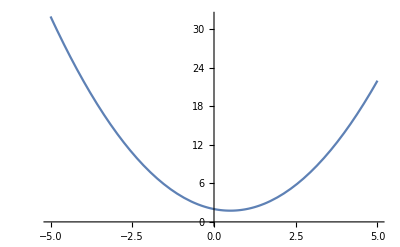

```mathematica
Plot[x^2-x+2,{x,-5,5}]
```

The first argument may also be based on a named function, as the following examples illustrate. The essential requirement is that the first argument must evaluate to a numeric value whenever the variable is assigned a value.

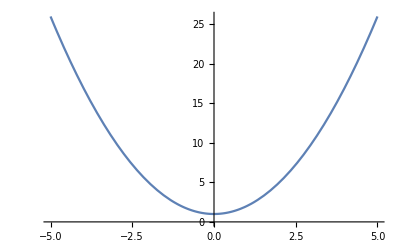

```mathematica
Plot[f[x],{x,-5,5}]
```

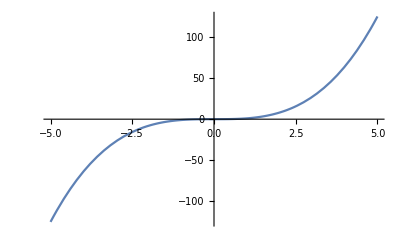

```mathematica
Plot[g[x],{x,-5,5}]
```

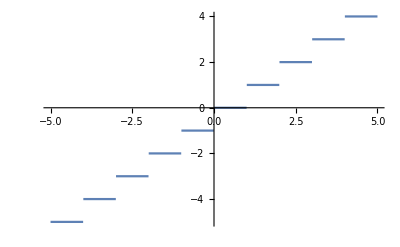

```mathematica
Plot[Floor[x],{x,-5,5}]
```

### Associations

For finite domains, an Association, introduced in Section 2.2 of this manual, is a natural way to represent a function. Another common approach is to use an indexed variable, which we use below to model recursively defined sequences.

For example, suppose f is the function whose domain is the set of students in a class and that maps each student to their grade on an exam. Let f be defined by f(Ann)=83, f(Bob)=79, f(Carla)=91, and f(Dave)=72. We model f as an Association named exams. Recall that an Association can be entered as a sequence of rules delimitated by <| on the left and |> on the right, with the arrow (→) entered as a hyphen followed by the greater than symbol (->).

```mathematica
exams=<|"Ann"->83,"Bob"->79,"Carlos"->91,"Delia"->72|>
```

<|Ann→83,Bob→79,Carlos→91,Delia→72|>

Once the indexed variable has been assigned, you can obtain the value f(Carla) as follows.

```mathematica
exams["Carlos"]
```

91

You can also modify values just by performing an assignment of the form association[key]=value. Moreover, with the association already defined, you can add new key–value pairs by making such an assignment.

```mathematica
exams["Ann"]=84
```

84

```mathematica
exams["Ernie"]=86
```

86

```mathematica
exams
```

<|Ann→84,Bob→79,Carlos→91,Delia→72,Ernie→86|>

The AssociateTo function can also be used to add key–value pairs. The first argument of AssociateTo is the symbol representing an association and the second is either a single Rule (→) or a list of rules. Note that AssociateTo modifies the association whose name is given as the first argument without explicit reassignment.

```mathematica
AssociateTo[exams,"Fred"->97]
```

<|Ann→84,Bob→79,Carlos→91,Delia→72,Ernie→86,Fred→97|>

```mathematica
AssociateTo[exams,{"Gigi"->98,"Hector"->88}]
```

<|Ann→84,Bob→79,Carlos→91,Delia→72,Ernie→86,Fred→97,Gigi→98,Hector→88|>

```mathematica
exams
```

<|Ann→84,Bob→79,Carlos→91,Delia→72,Ernie→86,Fred→97,Gigi→98,Hector→88|>

#### Domain and Range

Since associations represent finite functions, we can check their properties computationally. First, we will find the domain (that is, the domain of definition) and range of a function defined as an association. In the exams function, the students’ names (Ann, Bob, etc.) form the domain (called the keys) and the scores (84, 79, etc.) are the range (or values).

The Wolfram Language provides functions for extracting the list of keys and values of an association. Namely, Keys and Values both accept an association as their argument and return the list of keys and values, respectively. To define functions for obtaining the domain and range, we merely apply those functions and then apply Union to the resulting list, since we conceive of domain and range as sets rather than lists.

```mathematica
domain[f_Association]:=Union[Keys[f]];
range[f_Association]:=Union[Values[f]]
```

Using these functions, we can easily find the domain and range of exams.

```mathematica
domain[exams]
```

{Ann,Bob,Carlos,Delia,Ernie,Fred,Gigi,Hector}

```mathematica
range[exams]
```

{72,79,84,86,88,91,97,98}

#### Injective and Surjective

We will create a few more examples and then write functions to check for injectivity and surjectivity. The examples below correspond to the functions f_1(x)=x^2, f_2(x)=x^3, and f_3(x)=|x| on the domain D={-5,-4,…,5}.

Thus far, we have usually defined associations by manually entering all of the key–value pairs. The one exception was the fuzzyIntersection function in the previous section. There, we used AssociationThread to take a list of keys and a list of values and form the association by pairing corresponding elements from the two lists. Here, we will use AssociationMap to apply a function to a list of keys in order to compute the corresponding values. Specifically, the domain {-5,-4,...,4,5} is the list of keys for the associations. The function f_1, as an example, will be modeled by the association with the rules -5→f_1(-5), -4→f_1(-4), etc.

AssociationMap accepts a function as its first argument. This is a function in the Wolfram Language sense, so we need to either define a function and assign it to a symbol or enter a pure Function as the first argument. We will illustrate both options below. The second argument will be the domain of our function, that is, the list of keys. Recall that Range with two integer arguments forms the list of integers from the first argument through the second argument.

```mathematica
f1formula[x_]:=x^2;
f1=AssociationMap[f1formula,Range[-5,5]]
```

<|-5→25,-4→16,-3→9,-2→4,-1→1,0→0,1→1,2→4,3→9,4→16,5→25|>

```mathematica
f2=AssociationMap[#^3&,Range[-5,5]]
```

<|-5→-125,-4→-64,-3→-27,-2→-8,-1→-1,0→0,1→1,2→8,3→27,4→64,5→125|>

```mathematica
f3=AssociationMap[Abs,Range[-5,5]]
```

<|-5→5,-4→4,-3→3,-2→2,-1→1,0→0,1→1,2→2,3→3,4→4,5→5|>

Observe that for f_1(x)=x^2, we used the symbol we created for the formula, and for f_3(x)=|x|, we used the name of the built-in absolute-value function Abs. Typically, when a Wolfram Language function requires another function as an argument, it expects the symbol that names the function without an argument.

The domain and range functions defined earlier produce the expected results.

```mathematica
domain[f1]
```

{-5,-4,-3,-2,-1,0,1,2,3,4,5}

```mathematica
range[f1]
```

{0,1,4,9,16,25}

We can check to see if a function represented by an association is surjective for a specified codomain by comparing the codomain to the range.

```mathematica
surjectiveQ[f_Association,codomain_List]:=range[f]==Union[codomain]
```

Note that we applied Union to the second argument to provide assurance that both sets being compared are without duplicates and in standard order (recall that range applies Union before ending).

As expected, f1 is not onto {0,1,2,3,4,5}, but f3 is.

```mathematica
surjectiveQ[f1,Range[0,5]]
```

False

```mathematica
surjectiveQ[f3,Range[0,5]]
```

True

We can check for injectivity by making sure that no value is repeated. The easiest way to do this is to check that the number of values in the result of range is the same as the number of rules in the association. Note that Length applied to an association gives the number of rules.

```mathematica
injectiveQ[f_Association]:=Length[range[f]]==Length[f]
```

This function will confirm that f1 is not injective but that f2 is.

```mathematica
injectiveQ[f1]
```

False

```mathematica
injectiveQ[f2]
```

True

#### Graphing a Function Defined as an Indexed Variable

Finally, we see how to graph a function defined by an association. The Wolfram Language makes this quite easy with the use of ListPlot. The most common use of ListPlot is to provide it with a list of x–y pairs (represented as a list of 2-element lists) to display a plot of the points.

Conveniently, ListPlot also can accept an association as its first argument, and, provided that the association’s keys and values are all numeric, the output will be the graph with keys plotted on the horizontal axis and values on the vertical.

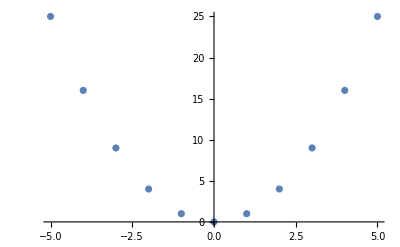

```mathematica
ListPlot[f1]
```

Two common options used in conjunction with ListPlot are PlotRange and Joined. PlotRange can be used to explicitly choose the span in both the horizontal and vertical directions. To use the PlotRange option, give PlotRange->{{xmin,xmax},{ymin,ymax}} as an argument to ListPlot. You can substitute All for either of the x or y ranges to include all the data.

The Joined option causes Mathematica to “connect the dots.” You invoke it by including Joined->True in the call to ListPlot.

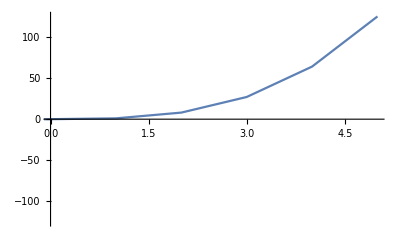

```mathematica
ListPlot[f2,Joined->True,PlotRange->{{0,5},All}]
```

The PlotStyle option can be used to set a variety of visual aspects of the plot including color (e.g., Red, Blue, Green, etc.) and point size (PointSize), as illustrated below.

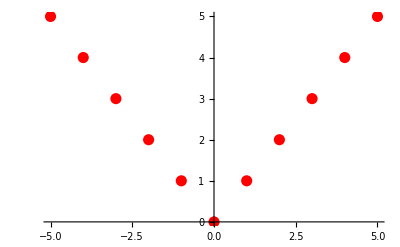

```mathematica
ListPlot[f3,PlotStyle->{Red,PointSize[.02]}]
```

### Some Important Functions

We have already seen that the Wolfram Language has a built-in function Floor. It also includes Ceiling for computing the ceiling of a real number.

```mathematica
Floor[2.7]
```

2

```mathematica
Ceiling[2.7]
```

3

The Wolfram Language contains some other related functions. The Round function rounds a number to the nearest integer. The IntegerPart and FractionalPart functions, as their names imply, compute the integral or fractional part of a real number.

```mathematica
Round[2.7]
```

3

```mathematica
IntegerPart[2.7]
```

2

```mathematica
IntegerPart[-2.7]
```

-2

```mathematica
FractionalPart[2.7]
```

0.7

The textbook also discusses the factorial function. In Mathematica, you compute the factorial of a number using the Factorial (!) function, typically with the operator !.

```mathematica
6!
```

720

```mathematica
Factorial[6]
```

720

## 2.4 Sequences and Summations

In this section, we will see how Mathematica can be used to create and manipulate sequences, and in particular, we will see a way to generate the terms of a recurrence sequence. We will also look at summations and see how Mathematica’s symbolic computation abilities can be used to explore both finite and infinite series.

In the Wolfram Language, you represent a finite sequence as a list. The “empty list” is represented by the expression {}.

There are a wide variety of ways that lists can be created in the Wolfram Language. Here, we will describe three of the most important: the Table function, Append and related functions, and the Sow and Reap functions.

### Building Lists: the Table Function

We have already seen several examples of the Table function. We briefly summarize some of the ways it can be called.

The most common way to use Table is demonstrated in the following example, which creates the first 11 terms of the geometric sequence a, a·r, a·r^2,… for a=3 and r=4.

```mathematica
Table[3*4^i,{i,0,10}]
```

{3,12,48,192,768,3072,12288,49152,196608,786432,3145728}

The first argument is an expression which may involve an index variable, in this case i. The second argument is a list whose elements are the variable and the minimum and maximum values for the index variable.

The minimum value can be omitted, in which case it will default to 1. The following shows the sequence beginning with i=1.

```mathematica
Table[3*4^i,{i,10}]
```

{12,48,192,768,3072,12288,49152,196608,786432,3145728}

By including three numeric arguments, in addition to the name of the variable, you can control the step, that is, the amount by which the index variable is incremented. For example, the expression below will produce every other term of the same geometric sequence as above.

```mathematica
Table[3*4^i,{i,0,10,2}]
```

{3,48,768,12288,196608,3145728}

The bounds of the range for the index variable and the step do not necessarily need to be integers. For example, the following produces the list of numbers beginning with 2.3, increasing by 0.25, up to an upper bound of 5.1. Note that the maximum is not included.

```mathematica
Table[i,{i,2.3,5.1,.25}]
```

{2.3,2.55,2.8,3.05,3.3,3.55,3.8,4.05,4.3,4.55,4.8,5.05}

The Range function can be thought of as an abbreviation of Table for situations like the previous example, where you simply want to produce the list of numbers without evaluating an expression. It accepts one, two, or three numerical arguments, with the same interpretation as the numeric elements of the second argument of Table.

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[0,10]
```

{0,1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[0,10,2]
```

{0,2,4,6,8,10}

Table can also be used to evaluate an expression for a specific list of values. This is illustrated in the example below, which finds the squares of the first six primes. Note that the second argument in this formulation is a list with two elements: the first is the name of the index variable and the second is the list of values to be substituted.

```mathematica
Table[i^2,{i,{2,3,5,7,11,13}}]
```

{4,9,25,49,121,169}

The order of the provided list determines the order of the output. For example, if we rearrange the primes, the output is affected accordingly.

```mathematica
Table[i^2,{i,{2,5,7,13,11,3}}]
```

{4,25,49,169,121,9}

Apply Union to the result if you want to think about the output as a set or to impose numerical order on the output.

```mathematica
Union[Table[i^2,{i,{2,5,7,13,11,3}}]]
```

{4,9,25,49,121,169}

Table can handle more than one variable—just provide an additional argument specifying the values for each variable. For example, the following finds the values of 2^i 3^j for i from 2 to 12 by 3 and j∈{1,2,3}.

```mathematica
Table[2^i*3^j,{i,2,12,3},{j,{1,2,3}}]
```

{{12,36,108},{96,288,864},{768,2304,6912},{6144,18432,55296}}

Note that the result is a list of lists, with the sublists composed of the values computed from a single value of the first variable. That is, the first sublist is the output with i=2 and all values of j, the second sublist is the output with i=5 (the second value of i) and all the values of j, etc.

### Building Lists: the Append Function

To add an element to the end of a list, use the Append or AppendTo function. The Append function requires two arguments: the first is a list and the second is a single object to be added to the end of the list. For example, to add 4 to the end of the list {1,2,3}, apply Append to {1,2,3} and 4.

```mathematica
Append[{1,2,3},4]
```

{1,2,3,4}

The Append function can also accept a symbol storing a list as its first argument. However, it will not modify the stored list.

```mathematica
exampleList={1,2,3}
```

{1,2,3}

```mathematica
Append[exampleList,4]
```

{1,2,3,4}

```mathematica
exampleList
```

{1,2,3}

In order to have the new list stored in the name, you either need to explicitly reassign the result of Append back to the name, or you can use AppendTo which automatically updates the list.

```mathematica
exampleList=Append[exampleList,4]
```

{1,2,3,4}

```mathematica
exampleList
```

{1,2,3,4}

```mathematica
AppendTo[exampleList,5]
```

{1,2,3,4,5}

```mathematica
exampleList
```

{1,2,3,4,5}

Note that AppendTo requires that the first argument be a symbol. If you try to call it with an explicit list as the first argument, it will raise an error.

Related to Append and AppendTo are Prepend and PrependTo, which have the same syntax but add the element to the front of the list rather than the end.

```mathematica
PrependTo[exampleList,6]
```

{6,1,2,3,4,5}

Earlier in this manual, we saw that you can modify elements of a list by using the Part operator ([[…]]) and assigning a new value. The following changes the third element of our list to 7.

```mathematica
exampleList[[3]]=7
```

7

```mathematica
exampleList
```

{6,1,7,3,4,5}

The ReplacePart function can also be used to modify an element of a list, but is more general. The most basic syntax of ReplacePart involves a list and a rule of the form part->new. The output is the list with the entry at position part replaced by the expression new.

```mathematica
ReplacePart[exampleList,4->11]
```

{6,1,7,11,4,5}

Note that this does not modify the list stored in exampleList without explicit reassignment. There are a variety of other syntax options for the second argument of ReplacePart to produce more general effects. These will be discussed only when they are needed.

If you wish to add an element in the middle of the list, rather than overwriting an element, you use the Insert function with the list, the element to be added, and the index at which it is to appear. The other members of the list are shifted to accommodate the new one. Note that Insert does not modify a list stored as a symbol without explicitly reassigning it.

```mathematica
exampleList=Insert[exampleList,8,4]
```

{6,1,7,8,3,4,5}

Similarly, you can remove an element by calling Delete with the list and the position of the element to be removed. Like Insert, Delete does not automatically modify a variable.

```mathematica
exampleList=Delete[exampleList,2]
```

{6,7,8,3,4,5}

### Building Lists: Sow and Reap

The AppendTo (or Append) function can be used within a function to build a list. For example, the function defined below builds the first n+1 terms of the geometric sequence with parameters a and r.

```mathematica
geometricSequence[a_,r_,n_]:=Module[{S={},i},
Do[AppendTo[S,a*r^i],{i,0,n}];
S
]
```

```mathematica
geometricSequence[3,4,10]
```

{3,12,48,192,768,3072,12288,49152,196608,786432,3145728}

However, the pair of functions Sow and Reap tend to be a much more efficient approach to this task. The following recreates the above function using this method.

```mathematica
geometricSequence2[a_,r_,n_]:=Module[{i},
Reap[
Do[Sow[a*r^i],{i,0,n}]
]
]
```

```mathematica
geometricSequence2[3,4,10]
```

{Null,{{3,12,48,192,768,3072,12288,49152,196608,786432,3145728}}}

Let us analyze the function above. The Reap function accepts any expression (or multiple expressions separated by semicolons) as its argument. Its result is a two-member list, the first element of which is the output obtained by evaluating the expression. In the above, Do always outputs Null, so that is the first element of the output.

The second element of the output of Reap is a list of lists, whose members are determined by the use of Sow within the Reap. In the simplest form, as above, the second element of the output is a list which contains a single list comprised of all of the results of evaluating Sow. That is, each time Sow is encountered, its argument is evaluated and added to this list. We can modify geometricSequence2 to produce the same output as geometricSequence just by accessing the [[2,1]] position of the result of Reap.

```mathematica
geometricSequence2[a_,r_,n_]:=Module[{i},
Reap[
Do[Sow[a*r^i],{i,0,n}]
][[2,1]]
]
```

```mathematica
geometricSequence2[3,4,10]
```

{3,12,48,192,768,3072,12288,49152,196608,786432,3145728}

While the Sow and Reap approach may seem more complicated than using AppendTo, the resulting function is significantly more efficient. The Timing function returns the list whose first element is the time it took to execute the expression and the second argument is the output. The semicolons suppress the output of the functions so we can focus on the time.

```mathematica
Timing[geometricSequence[3,4,10000];]
```

{0.205748,Null}

```mathematica
Timing[geometricSequence2[3,4,10000];]
```

{0.02809,Null}

The second element of the output of Reap is always a list of lists. This is to allow for more fine-tuned creation of lists through the use of optional tags. For example, you could separate the terms in our geometric sequence based on whether their index is even or odd as follows.

```mathematica
Reap[
Do[If[EvenQ[i],Sow[3*4^i,even],Sow[3*4^i,odd]],
{i,0,10}]
]
```

{Null,{{3,48,768,12288,196608,3145728},{12,192,3072,49152,786432}}}

The result of Reap is still a two-element list with first element Null (the output of Do). However, the second element of Reap’s output is now a list with two sublists: one consisting of the elements sown with tag even and one list for those sown with tag odd.

The second argument of Sow can, in fact, be a list of tags, in which case elements can appear in more than one sublist. For example, the following produces three lists (as sublists in the second element of the output): the even-indexed terms, the odd-indexed terms, and all of the terms.

```mathematica
Reap[
Do[If[EvenQ[i],
Sow[3*4^i,{all,even}],
Sow[3*4^i,{all,odd}]],
{i,0,10}]
]
```

{Null,{{3,12,48,192,768,3072,12288,49152,196608,786432,3145728},{3,48,768,12288,196608,3145728},{12,192,3072,49152,786432}}}

Reap also accepts a second argument as a way to limit which tags are included in the output. For example, the following will output only the even-indexed terms.

```mathematica
Reap[
Do[If[EvenQ[i],
Sow[3*4^i,{all,even}],
Sow[3*4^i,{all,odd}]],
{i,0,10}]
,even]
```

{Null,{{3,48,768,12288,196608,3145728}}}

The second argument to Reap is actually a pattern, not a tag, so you can use pattern construction elements, such as the vertical bar (|) to include options. The result will be the list of all lists whose tags match the pattern.

```mathematica
Reap[
Do[If[EvenQ[i],
Sow[3*4^i,{all,even}],
Sow[3*4^i,{all,odd}]],
{i,0,10}]
,all|even]
```

{Null,{{3,12,48,192,768,3072,12288,49152,196608,786432,3145728},{3,48,768,12288,196608,3145728}}}

The Reap function can also accept a third argument: a function of two arguments. For each tag matching the pattern in Reap’s second argument, the function is applied to the tag and the list associated with that tag. One useful construction is shown below and has the effect of turning the second element of the result into a list of rules identifying the tags with the associated lists.

```mathematica
Reap[
Do[If[EvenQ[i],
Sow[3*4^i,{all,even}],
Sow[3*4^i,{all,odd}]],
{i,0,10}]
,_,Rule]
```

{Null,{all→{3,12,48,192,768,3072,12288,49152,196608,786432,3145728},even→{3,48,768,12288,196608,3145728},odd→{12,192,3072,49152,786432}}}

Note that the second argument used above is a blank (_), ensuring that all tags are included in the output. The head Rule is given as the third argument, and it is applied to each tag and associated list creating three rules in the output. By storing this list of rules as a symbol, and then using a ReplaceAll (/.) in conjunction with a Set (=) that identifies a symbol with a tag, you can assign one of the lists to a symbol.

```mathematica
ruleList=Reap[
Do[If[EvenQ[i],
Sow[3*4^i,{all,even}],
Sow[3*4^i,{all,odd}]],
{i,0,10}]
,_,Rule][[2]]
```

{all→{3,12,48,192,768,3072,12288,49152,196608,786432,3145728},even→{3,48,768,12288,196608,3145728},odd→{12,192,3072,49152,786432}}

```mathematica
evenList=even/.ruleList
```

{3,48,768,12288,196608,3145728}

```mathematica
evenList
```

{3,48,768,12288,196608,3145728}

You might wonder about using Set instead of Rule as the final argument to Reap. This will have the effect of assigning the appropriate lists to the symbols used as the tags. However, there is a significant drawback. Specifically, once the Reap expression has been evaluated and the assignment of tags to lists has been made, you can no longer use those symbols as tags without first removing the assignment with Unset (=.) or Clear. This does not, however, apply in contexts where the tags are made local, such as inside of a Module, as is done below.

```mathematica
geometricSequence3[a_,r_,n_]:=Module[{i,seq},
Reap[
Do[Sow[a*r^i,seq],{i,0,n}]
,_,Set];
seq
]
```

```mathematica
geometricSequence3[3,4,10]
```

{3,12,48,192,768,3072,12288,49152,196608,786432,3145728}

In geometricSequence3, the symbol seq is localized to the module. It is then used as the tag to Sow. The enclosing Reap uses the Set function, which has the effect of setting seq to the list containing the geometric sequence. Once the Reap function is closed, we have the function evaluate seq so that it becomes the output.

Note that making seq local means that it does not store the sequence after the function is complete and that it can be reused. If we did not make it local, the function could only be executed once. Consequently, you should use this approach with caution.

### Recurrence Relations

Next, we will see how we can use Mathematica to explore sequences that arise from recurrence relations. We will go into much more depth, especially in regards to the Wolfram Language’s functions related to solving recurrence relations, in Chapter 8. Here, we will only explore how we can have Mathematica compute terms of sequences defined by recurrence relations.

As an example, consider the Fibonacci sequence, which has recurrence relation f_n=f_(n-1)+f_(n-2) and initial conditions f_1=0 and f_2=1. (Note that the textbook uses 0 as the first index for a sequence, but the Wolfram Language uses 1 as the first index for lists, and we will follow the Wolfram Language convention.) To produce this sequence in Mathematica, we can use an indexed variable.

The basic idea of an indexed variable is that the Wolfram Language allows us to use the notation of functions in a very flexible way. For example, we could define a function that squares its argument.

```mathematica
xsquared[x_]:=x^2
```

We might then decide that, for this function, the input value 0 should return -1. We could redefine the function with a an If statement or Switch. But the Wolfram Language allows us to simply tell it that xsquared[0] = -1.

```mathematica
xsquared[0]=-1
```

-1

When we call xsquared on an argument, Mathematica will check which definition is most appropriate and return the relevant value.

```mathematica
xsquared[0]
```

-1

```mathematica
xsquared[5]
```

25

To see the entire definition of the indexed variable, you can use the Definition function or the ? operator, as shown below.

```mathematica
?xsquared
```

Global`xsquared

xsquared[0]=-1
 
xsquared[x_]:=x^2

Back to the Fibonacci sequence. Define a function named fib to represent the recurrence relation.

```mathematica
fib[n_]:=fib[n-1]+fib[n-2]
```

The left-hand side of this definition indicates that when it’s asked to evaluate fib on an argument, it should perform the computations on the right-hand side with n replaced by the given argument.

Next, we set the initial values.

```mathematica
fib[1]=0;
fib[2]=1;
```

Now, Mathematica will compute values of the sequence.

```mathematica
fib[8]
```

13

To display a list of elements of the sequence, use the Table function.

```mathematica
Table[fib[i],{i,20}]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181}

While the above approach for calculating recurrence relations is convenient and intuitive, it is also very inefficient. Observe that the definition of fib contains only the recurrence relation and initial conditions.

```mathematica
?fib
```

Global`fib

fib[1]=0
 
fib[2]=1
 
fib[n_]:=fib[n-1]+fib[n-2]

This tells us that computed values are not being stored, and so Mathematica must recompute all but the first two values of the sequence every time a value is desired. We can have Mathematica calculate the sequence more efficiently by having it remember all of the values it computes. This is demonstrated below.

```mathematica
fib2[1]=0;
fib2[2]=1;
fib2[n_]:=fib2[n]=fib2[n-1]+fib2[n-2];
```

We combined both the recurrence relation and initial conditions into one input expression. The above can be understood by distinguishing between the function fib2 and the indexed variable fib2. The first two lines assign values to the indexed variable fib2 with indices 1 and 2. The third line defines the function fib2. This function accepts one argument, named n. The body of the function is an assignment. Specifically, the function assigns a value to the indexed variable fib2. That value is obtained by either looking up or calculating earlier values.

This means that values will be stored as they are calculated. You can see this by looking at the definition of fib2 before and after evaluating fib2[3].

```mathematica
?fib2
```

Global`fib2

fib2[1]=0
 
fib2[2]=1
 
fib2[n_]:=fib2[n]=fib2[n-1]+fib2[n-2]

```mathematica
fib2[3]
```

1

```mathematica
?fib2
```

Global`fib2

fib2[1]=0
 
fib2[2]=1
 
fib2[3]=1
 
fib2[n_]:=fib2[n]=fib2[n-1]+fib2[n-2]

To illustrate the difference in performance, we see how long it takes to compute the 1000th Fibonacci number.

```mathematica
Timing[fib2[1000]]
```

{0.004021,26863810024485359386146727202142923967616609318986952340123175997617981700247881689338369654483356564191827856161443356312976673642210350324634850410377680367334151172899169723197082763985615764450078474174626}

Note that if we repeat the computation using fib2:

```mathematica
Timing[fib2[1000]]
```

{7.×10^-6,26863810024485359386146727202142923967616609318986952340123175997617981700247881689338369654483356564191827856161443356312976673642210350324634850410377680367334151172899169723197082763985615764450078474174626}

The total time taken drops dramatically. This is because Mathematica does not need to compute the value again, it just looks it up.

In comparison, consider the fib function applied to just 30.

```mathematica
Timing[fib[30]]
```

{1.08681,514229}

By storing the results of computations in a recursively generated sequence, we can get higher terms much more quickly.

Note that attempting to call fib2 with larger values, such as 10000, will raise an error, specifically:

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of fib2[8978-1]+fib2[8978-2].

Mathematica puts a limit on how far down a recursive definition it will go. This is to prevent Mathematica from crashing your computer by trying to exceed the machine’s stack space. To get around this, you can temporarily override the default recursion limit as in the following.

```mathematica
Block[{$RecursionLimit=10000},fib2[10000]]
```

The Block is similar to Module, in that it defines a scope and the first argument declares the variables local to that scope. In the above, Block is used to ensure that the change to the recursion limit is only temporary. The built-in recursion limit is there for a reason, and overriding it is inherently dangerous. If you were to change it permanently and then unwittingly execute an expression that caused a large recursive descent, you could crash your Mathematica session and lose your work.

Note that the purely recursive implementation fib cannot be reasonably used to compute the 10000th Fibonacci number. In fact, to compute the 10000th Fibonacci number, fib would need to be invoked approximately

```mathematica
Block[{$RecursionLimit=10000},N[fib2[9999]]]
```

1.28511566392983×10^2089

times in order to handle all the recursive sub-calls that are made. (The reader is encouraged to prove this fact.)

Even at a billion calls per second, this would require

```mathematica
fib2[9999]/1000000000.
```

1.28511566392983×10^2080

seconds, or

```mathematica
fib2[9999]/(1000000000.*60*60*24*365)
```

4.07507503782924×10^2072

years to complete.

### Summations

Finally, we will see how Mathematica can be used to compute with summations, both numerically for finite sums and symbolically for infinite sums.

To add a finite list of values, we use the Total function. Applied to a list, Total returns the sum.

```mathematica
Total[{1,2,4,6,9,11,14}]
```

47

The argument to Total can be a function that returns a list. For example, the following computes the sum of the integers from 1 to 100.

```mathematica
Total[Range[100]]
```

5050

The Wolfram Language also provides the function Sum, which can be used in place of composing Total and Table. Sum accepts arguments in the same form as Table, but instead of producing the list, it provides you with the sum of the sequence.

The first argument to Sum should be an expression involving a variable (the index of summation). The second argument is generally a list, whose first element is the index of summation (e.g., i) and whose other arguments specify the values that the index takes on, as detailed in the table below.

{i,i_max} | sum from i=1 to i_max
{i,i_min,i_max} | sum from i=i_min to i_max
{i,i_min,i_max,step} | sum from i=i_min to i_max by step
{i,list} | sum over i∈list

For example, to compute the sum of the squares of the first ten positive integers, ∑_(i=1)^10 i^2, we enter the following.

```mathematica
Sum[i^2,{i,10}]
```

385

To compute the sum ∑_(i=10)^30 1/i, you enter:

```mathematica
Sum[1/i,{i,10,30}]
```

2715762396337/2329089562800

Note that nested sums can be computed simply by providing additional specifications for the index of summation, just as is done with Table. Also note that there is a similar command for products, with identical syntax, called Product.

The Sum function can also be used for symbolic sums. For example, to compute the sum of the squares of the integers from 1 to n, that is, ∑_(i=1)^n i^2, you simply give the maximum for the index of summation as n, provided the symbol n has not been assigned a value.

```mathematica
Sum[i^2,{i,n}]
```

1/6 n (1+n) (1+2 n)

We also compute the sum of every other term from 0 to 2n in the general geometric series.

```mathematica
Sum[a*r^i,{i,0,2n,2}]
```

(a (-1+r^(2+2 Floor[n])))/(-1+r^2)

You are also allowed to use the symbol Infinity to compute infinite sums. The following computes ∑_(i=1)^∞ i x^(i-1).

```mathematica
Sum[i*x^(i-1),{i,Infinity}]
```

1/(-1+x)^2

You can confirm that these results match the formulas given in Table 2 of Section 2.4.

## 2.5 Cardinality of Sets

In this section, we will explore the countability of the positive rational numbers. In Example 4 of Section 2.5 of the text, it is shown that the positive rationals are countable by describing how to list them all. Here, we will use the Wolfram Language to implement this listing algorithm. We will also consider the following two questions. First, given a positive rational number, what is its position in the list? Second, given a positive integer, what rational number is located at that position within the list?

We begin by reviewing the description in Example 4. The first element of the list is the rational number 1/1. We next list the positive rationals p/q such that p+q=3. Then come the rationals with p+q=4, excluding 2/2, which is already in the list, being equivalent to 1/1. This continues for each n: we list the fractions p/q such that p+q=n, excluding those equivalent to fractions already in the list.

In our function, we refer to n as the stage, so that in stage 5, for example, we are listing the fractions p/q such that p+q=5. The stage n will range from 2 up to some maximum value. This maximum value of n will be the parameter to the function. We will implement this as a loop with index variable n.

Within each stage, that is, within the loop, we need to generate the rational numbers p/q and add them to the list, provided they are not already in it. We can rewrite p+q=n as p=n-q. By allowing q to range from 1 to n-1 and calculating p, we will produce all the potential rationals in stage n. The FreeQ function, which has the same syntax but opposite meaning of the MemberQ function discussed in Section 2.1 in relation to sets, will be used to avoid duplicates. Thus, for each q from 1 to n-1, we will form the fraction p/q (with p=n-q), use FreeQ to test whether this is already in our list of positive rationals, and, if not, add it to the list using AppendTo.

Here is the complete function.

```mathematica
listRationals[max_]:=Module[{L={},n,p,q},
For[n=2,n≤max,n++,
For[q=1,q≤n-1,q++,
p=n-q;
If[FreeQ[L,p/q],AppendTo[L,p/q]]
]
];
L
]
```

Applying this function with argument 6, we obtain the list of rationals through stage 6.

```mathematica
listRationals[6]
```

{1,2,1/2,3,1/3,4,3/2,2/3,1/4,5,1/5}

### Finding the Position Given a Positive Rational

Suppose we want to determine the position of a particular number within the list. Consider, for example, 29/35. Since the fraction is in lowest terms and 29+35=64, we know that this fraction would first appear in stage 64. Therefore, we compute the list up to stage 64.

```mathematica
ratsTo64=listRationals[64];
```

We suppress the output because this is a long list:

```mathematica
Length[ratsTo64]
```

1259

Now, we work backward from the end of the list until we find the desired fraction. A simple loop will help with this. Recall that the third argument to For allows us to specify how the index variable is changed each time. The decrement operator (--) causes the loop to step backward by 1 in each iteration. Once we find the location of the desired fraction, we want the loop to end and output the location of the fraction. We do this using a Throw and wrapping the entire loop in a Catch.

```mathematica
Catch[
For[i=1259,i≥1,i--,
If[ratsTo64[[i]]==29/35,Throw[i]]
]
]
```

1245

We can make this process into a function. Given a fraction, the Numerator and Denominator commands will extract the numerator and denominator, respectively.

```mathematica
Numerator[29/35]
```

29

```mathematica
Denominator[29/35]
```

35

Our function will accept a rational number as its argument. For the sake of robustness, we will ensure that the input is rational by insisting that the argument has head Rational, and we will also check that it is positive using a Condition (/;).

After confirming that the input is positive, we sum the results of Numerator and Denominator to determine the stage.

```mathematica
locateRational[r_Rational]/;r>0:=Module[{stage,L,i},
stage=Numerator[r]+Denominator[r];
L=listRationals[stage];
Catch[
For[i=Length[L],i≥1,i--,
If[L[[i]]==r,Throw[i]]
]
]
]
```

```mathematica
locateRational[75/197]
```

22566

### Finding the Rational in a Given Position

On the other hand, suppose we want to know which fraction is at a particular position. For instance, say we want to know which is the 100th fraction listed. If we knew which stage of the process would yield a list of at least 100 rational numbers, we could just generate the list up to that stage. We can guess and check until we find a stage that produced a long enough list.

#### Putting a Lower Bound on the Number of Stages

We can guide our guesses a bit, however. Remember that at stage 2, the process generates one fraction. At stage 3, it generates two fractions. At stage 4, it generates three fractions, although one of them is discarded because it is a repeat. At stage k, the process generates k-1 rational numbers, some of which may be discarded as repeats. Therefore, we know that, after stage n is complete, the number of rational numbers in our list contains at most ∑_(k=2)^n k-1 rational numbers. We can use the Sum function described in the previous section to find a formula for this summation.

```mathematica
Sum[k-1,{k,2,n}]
```

1/2 (-n+n^2)

In other words, the number of rational numbers in the list produced by listRationals at the conclusion of stage n is at most (n^2-n)/2. Define F(n) to be the number of positive rational numbers produced by the listRationals algorithm at the conclusion of stage n. Equivalently, F(n) is the number of distinct positive rational numbers p/q such that p+q≤n. We have determined that

F(n)≤(n^2-n)/2

Now, we return to the question of how many stages we need to compute in order to find the 100th rational number. We can restate this as follows: find n such that F(n)≥100. Combining our inequalities, we have that (n^2-n)/2≥100. The Wolfram Language’s Reduce command will solve the equation for us. The Reduce function requires two arguments: the expression to be simplified and the variable. (Note that since an approximation is sufficient, we apply the function N, so that the output will be given in decimal form. It is common to apply N in conjunction with the postfix operator (//).)

```mathematica
Reduce[(n^2-n)/2≥100,n]//N
```

n≤-13.651||n≥14.651

This indicates that a stage of 14 is not enough. However, it gives us a place to start guessing.

```mathematica
ratsTo15=listRationals[15];
```

```mathematica
Length[ratsTo15]
```

71

```mathematica
ratsto17=listRationals[17];
```

```mathematica
Length[ratsto17]
```

95

```mathematica
ratsTo18=listRationals[18];
```

```mathematica
Length[ratsTo18]
```

101

```mathematica
ratsTo18[[100]]
```

5/13

Thus, the 100th rational, in the order specified by this particular algorithm, is 5/13.

#### How Tight is the Bound?

We just saw how the formula (n^2-n)/2 is an upper bound for F(n), the number of positive rationals listed by the end of stage n. We conclude this section by exploring how good this bound is. In Section 2.3, we saw how to use the Plot function to graph functions. We use that technique to graph the upper bound (n^2-n)/2 from 1 to 100. Recall that the first argument to Plot is the function and the second is a list consisting of the name of the independent variable and the bounds.

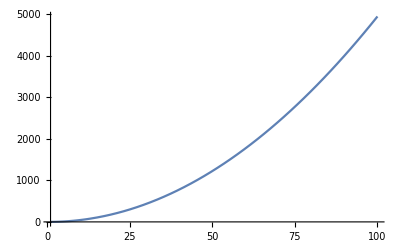

```mathematica
boundPlot=Plot[(n^2-n)/2,{n,1,100}]
```

Note that we stored the plot as the symbol boundPlot so as to be able to reuse it later.

To find the actual values of F(n), we need to find the size of the list returned by listRationals applied to n. In other words, we apply Length to the result of listRationals[n]. We use Table to form the list of these values with n ranging from 1 to 100.

```mathematica
dataTable=Table[Length[listRationals[n]],{n,100}];
```

The ListPlot function, applied to a list of values, will interpret the members of the list as the y-coordinates of points whose x-coordinates are the index of the number, which in this case is the value of n. We make this graph red using PlotStyle.

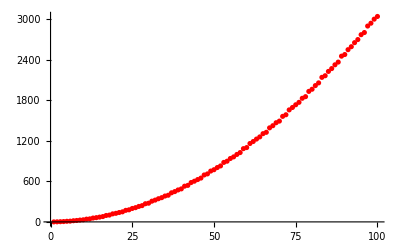

```mathematica
dataPlot=ListPlot[dataTable,PlotStyle->Red]
```

We can combine the two graphs using the Show function. The Show function allows you to combine graphics objects into one. We ensure that the entirety of both graphs is displayed by setting the option PlotRange to All.

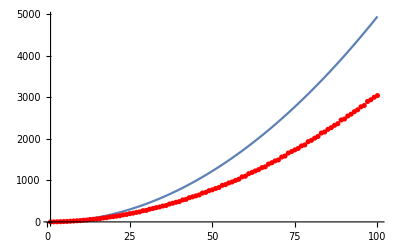

```mathematica
Show[boundPlot,dataPlot,PlotRange->All]
```

## 2.6 Matrices

The Wolfram Language provides extensive support for calculating with matrices. We begin this section by describing a variety of tools for constructing matrices in the Wolfram Language. Then, we will consider matrix arithmetic and operations on zero–one matrices.

### Constructing Matrices

In the Wolfram Language, matrices are represented as lists of lists, with the inner lists corresponding to the rows of the matrix. Consequently, the methods for working with lists apply also to matrices.

#### Specifying Matrices by Listing the Rows

The simplest way to create a matrix is to explicitly enter the values. The matrix is represented as a list of lists, with the first sublist consisting of the entries of the first row, the second sublist the second row, and so on.

```mathematica
m1={{1,2,3},{4,5,6}}
```

{{1,2,3},{4,5,6}}

To have Mathematica display the result in the typical format of a rectangular matrix, apply the function MatrixForm. This is often done in conjunction with the postfix operator (//).

```mathematica
m1//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6)

Be cautious, however, in using MatrixForm in conjunction with assignment. If you were to include the application of MatrixForm in the assignment of m1 above, then the MatrixForm head would be permanently associated with the symbol and other functions would not behave as expected.

Using Partition, you can enter the entries of the matrix in a single list and have Mathematica break it into rows of a size you specify. For example, the following creates the same matrix as m1.

```mathematica
m2=Partition[{1,2,3,4,5,6},3]
```

{{1,2,3},{4,5,6}}

The first argument is the list of all the entries in the matrix, from top left to bottom right. The second argument is the number of columns, that is, the number of elements in each row. Note that you can use Equal (==) to compare matrices, which confirms that these two matrices are identical.

```mathematica
m1==m2
```

True

#### Creating Matrices with Table

The Table function can be used to create matrices. The first argument to Table will involve two variables, and there will be two table variable specifications, with the first associated to the columns and the second to the rows.

For example, the following creates the 4 by 5 matrix whose entries are the sum of their indices.

```mathematica
m3=Table[i+j,{i,4},{j,5}];
MatrixForm[m3]
```

(2 | 3 | 4 | 5 | 6
3 | 4 | 5 | 6 | 7
4 | 5 | 6 | 7 | 8
5 | 6 | 7 | 8 | 9)

Note that the iteration specifications determine the values used while calculating the entries, but their position within the matrix is determined by the order in which the iteration occurs. Below, we create the matrix whose entries are x^i y^j with the exponents to x ranging from 3 to 5 in decreasing order and the exponents of y determined by the list {3,7,2,5}. We emphasize that the first iteration specification corresponds to the columns of the matrix and the second to the rows, which is clear from this output.

```mathematica
m4=Table[x^i y^j,{i,5,3,-1},{j,{3,7,2,5}}];
m4//MatrixForm
```

(x^5 y^3 | x^5 y^7 | x^5 y^2 | x^5 y^5
x^4 y^3 | x^4 y^7 | x^4 y^2 | x^4 y^5
x^3 y^3 | x^3 y^7 | x^3 y^2 | x^3 y^5)

#### Manipulating and Combining Matrices

The IdentityMatrix function takes a positive integer as its argument and produces an identity matrix of that size.

```mathematica
IdentityMatrix[3]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

The ConstantArray function can be used to create a list (including a matrix) all of whose entries are identical. Its first argument is the constant with which to populate the list and the second argument specifies the size of the structure.

If the second argument is an integer, ConstantArray produces a list of that length.

```mathematica
ConstantArray[x,5]
```

{x,x,x,x,x}

If the second argument is a list consisting of a pair of integers, it produces a matrix of that size.

```mathematica
m5=ConstantArray[0,{4,3}];
m5//MatrixForm
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

We can then modify the entries of the constant matrix using the Part ([[…]]) operator. Note that the locations within the matrix specified with the Part ([[…]]) operator are consistent with the usual mathematical notation, that is, row then column.

```mathematica
m5[[1,1]]=5;
m5[[1,3]]=3;
m5[[3,2]]=7;
m5[[4,1]]=-2;
m5//MatrixForm
```

(5 | 0 | 3
0 | 0 | 0
0 | 7 | 0
-2 | 0 | 0)

Provided the dimensions match, you can merge two matrices—effectively gluing one next to the other or one on top of the other—with the Join function.

For example, if you have two matrices with the same number of columns, you can stack one on top of the other by calling Join on the two matrices. The top matrix should be given as the first argument.

```mathematica
Join[IdentityMatrix[3],m5]//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1
5 | 0 | 3
0 | 0 | 0
0 | 7 | 0
-2 | 0 | 0)

Given two matrices with the same number of rows, you can combine them side by side by calling Join with the two matrices as the first two arguments and the number 2 as a third argument.

```mathematica
Join[IdentityMatrix[3],m4,2]//MatrixForm
```

(1 | 0 | 0 | x^5 y^3 | x^5 y^7 | x^5 y^2 | x^5 y^5
0 | 1 | 0 | x^4 y^3 | x^4 y^7 | x^4 y^2 | x^4 y^5
0 | 0 | 1 | x^3 y^3 | x^3 y^7 | x^3 y^2 | x^3 y^5)

The Join function is in fact a very useful general function. It accepts as arguments a number of expressions and an optional integer, provided that the expressions all have the same head, for example, List. If the optional integer is not present, Join combines the expressions into one expression with that common head. The optional argument specifies the level at which to join. By giving the argument 2, it means that rather than joining the expressions, it joins their corresponding subexpressions.

Finally, the ArrayPad function can be used to extend a matrix in any direction by padding it with a constant. The first argument is the existing list or matrix. The second argument specifies the dimensions of the padding, that is, how many additional rows or columns to add on each side. The third (optional) argument specifies the object to pad with. The padding defaults to 0.

The most general form of the second argument, the dimensions of the padding, is a list of the form {{top,bottom},{left,right}}, where top stands for the number of rows to add above the matrix, etc. For example, the following adds 1s along the bottom and right of the matrix m4 and two columns along the left.

```mathematica
ArrayPad[m4,{{0,1},{2,1}},1]//MatrixForm
```

(1 | 1 | x^5 y^3 | x^5 y^7 | x^5 y^2 | x^5 y^5 | 1
1 | 1 | x^4 y^3 | x^4 y^7 | x^4 y^2 | x^4 y^5 | 1
1 | 1 | x^3 y^3 | x^3 y^7 | x^3 y^2 | x^3 y^5 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1)

The second argument can be simplified when the padding is consistent. For example, to add columns of 1s along the bottom and right, rather than providing {{0,1},{0,1}}, you can simply use {0,1}. The correct interpretation of this is that we are adding nothing at the beginning and one entry at the end of every level (row and column).

```mathematica
ArrayPad[m4,{0,1},1]//MatrixForm
```

(x^5 y^3 | x^5 y^7 | x^5 y^2 | x^5 y^5 | 1
x^4 y^3 | x^4 y^7 | x^4 y^2 | x^4 y^5 | 1
x^3 y^3 | x^3 y^7 | x^3 y^2 | x^3 y^5 | 1
1 | 1 | 1 | 1 | 1)

If you give just an integer as the second argument, then that number of elements will be added in every direction.

```mathematica
ArrayPad[m4,2,1]//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | x^5 y^3 | x^5 y^7 | x^5 y^2 | x^5 y^5 | 1 | 1
1 | 1 | x^4 y^3 | x^4 y^7 | x^4 y^2 | x^4 y^5 | 1 | 1
1 | 1 | x^3 y^3 | x^3 y^7 | x^3 y^2 | x^3 y^5 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

### Matrix Arithmetic

The textbook defines addition and multiplication of matrices. The Wolfram Language implements these operations on matrices in a fairly intuitive way. To add two matrices, you use the + operator, as you would expect.

```mathematica
m6={{1,2,3},{4,5,6}};
m6//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6)

```mathematica
m7={{-2,3,-1},{1,5,2}};
m7//MatrixForm
```

(-2 | 3 | -1
1 | 5 | 2)

```mathematica
m6+m7//MatrixForm
```

(-1 | 5 | 2
5 | 10 | 8)

The Wolfram Language’s syntax for multiplying a matrix by a scalar is also intuitive.

```mathematica
3*m7//MatrixForm
```

(-6 | 9 | -3
3 | 15 | 6)

This produces the matrix whose entries are three times the entries of m7.

Matrix multiplication is computed using the Dot (.) operator, not the Times (*) operator.

```mathematica
m8={{3,6,11,1},{-2,5,2,0},{4,8,9,-3}};
m8//MatrixForm
```

(3 | 6 | 11 | 1
-2 | 5 | 2 | 0
4 | 8 | 9 | -3)

```mathematica
m9={{2,5},{1,-2},{3,7},{-1,0}};
m9//MatrixForm
```

(2 | 5
1 | -2
3 | 7
-1 | 0)

```mathematica
m8.m9//MatrixForm
```

(44 | 80
7 | -6
46 | 67)

The reason that addition and scalar multiplication work in the natural way is that the functions Plus and Times have the Listable attribute, which means that they are automatically threaded over lists (and thus matrices). However, since Times is Listable, Mathematica would compute the product m6*m7 by multiplying corresponding entries, even though this is not the correct operation mathematically. Hence, the Dot (.) operator is needed.

### Powers and Transposes of Matrices

Computing powers of square matrices is done with the MatrixPower function. (Note that the usual Power (^) operator will compute the power of each element of the matrix.) As you would expect, the first argument is the matrix and the second the exponent.

```mathematica
m10={{1,2,3},{4,5,6},{7,8,9}};
m10//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
MatrixPower[m10,5]//MatrixForm
```

(121824 | 149688 | 177552
275886 | 338985 | 402084
429948 | 528282 | 626616)

Note that if the exponent is negative, the result will be the power of the inverse, provided one exists.

The transpose of a matrix can be computed with the Transpose function.

```mathematica
Transpose[m10]//MatrixForm
```

(1 | 4 | 7
2 | 5 | 8
3 | 6 | 9)

### Zero–One Matrices

With Mathematica, we can create and manipulate zero–one matrices as well. In particular, we will consider how to compute the meet, join, and Boolean product of zero–one matrices.

Recall from the previous chapter that the Wolfram Language provides the BitAnd and BitOr functions for computing the bitwise AND and OR operations. In addition, recall from the textbook that the meet and join of two zero–one matrices correspond to computing the bitwise AND and OR on corresponding entries. Since the BitAnd and BitOr functions have the Listable attribute, they automatically thread over lists. Thus, applying BitAnd and BitOr to matrices of the same dimension exactly computes the meet and join.

Below, we define two example matrices and use BitOr to compute their meet. The reader can verify that the result is correct.

```mathematica
zerooneEx1={{1,0,1},{1,1,0},{0,1,0}};
zerooneEx1//MatrixForm
```

(1 | 0 | 1
1 | 1 | 0
0 | 1 | 0)

```mathematica
zerooneEx2={{1,0,0},{1,1,1},{0,0,0}};
zerooneEx2//MatrixForm
```

(1 | 0 | 0
1 | 1 | 1
0 | 0 | 0)

```mathematica
BitOr[zerooneEx1,zerooneEx2]//MatrixForm
```

(1 | 0 | 1
1 | 1 | 1
0 | 1 | 0)

#### Type Checking Zero–One Matrices

Recall from Section 1.1 of this manual that the BitAnd and BitOr functions will accept as input any integers, not just the bits 0 and 1. It is a good habit, when writing functions, to ensure that the input to a function is of the right type. Otherwise, the function may attempt to operate on the bad input and produce output without telling you that the input was bad. To prevent this, you use “type checking.” Here, we will see how to type check zero–one matrices and build those checks into functions meet and join. The body of these functions will simply be applications of BitAnd and BitOr, respectively.

Our test will be based on the Wolfram Language’s built-in MatrixQ function. The MatrixQ function accepts an expression and returns true if the object is a list of lists that represents a rectangular matrix and false otherwise. It also accepts, as a second optional argument, a function in one argument that imposes a condition on the elements of the matrix. Specifically, the second argument is a function that is applied to each element of the matrix and the MatrixQ function only returns true if the first argument is a matrix and every element of the matrix satisfies the test specified by the second argument.

For example, the following checks that the zerooneEx1 matrix is a matrix of integers, using IntegerQ as the test function.

```mathematica
MatrixQ[zerooneEx1,IntegerQ]
```

True

However, given a matrix with even one entry that is not an integer, it will return false.

```mathematica
MatrixQ[{{1,2},{3/4,5}},IntegerQ]
```

False

To check whether an expression represents a zero–one matrix, we will need to design a function that returns true when its input is 0 or 1 and false otherwise. It is easy to create such a function using a pure function. Recall from Section 2.3 of this manual that a pure function of one argument is constructed as an expression using the Slot (#) in place of the argument and ending with an ampersand, that is, the Function (&) operator. To test whether the argument is 0 or 1, we just need to evaluate the proposition (x=0)∨(x=1).

Here is the definition of zeroOneMatrixQ.

```mathematica
zeroOneMatrixQ[m_]:=MatrixQ[m,(#==0)||(#==1)&]
```

This function will return true for a zero–one matrix, but false if given an input that is not a rectangular matrix or contains elements that are not 0 or 1.

```mathematica
zeroOneMatrixQ[zerooneEx1]
```

True

```mathematica
zeroOneMatrixQ[{{1,0,0},{0,1}}]
```

False

```mathematica
zeroOneMatrixQ[{{1,0,0},{0,1,2}}]
```

False

We can now use zeroOneMatrixQ to impose type checking in order to build functions meet and join. We use the _? construction to ensure that the arguments are zero–one matrices.

```mathematica
meet[a_?zeroOneMatrixQ,b_?zeroOneMatrixQ]:=BitAnd[a,b]
```

```mathematica
join[a_?zeroOneMatrixQ,b_?zeroOneMatrixQ]:=BitOr[a,b]
```

These functions now perform their respective operations, but only on zero–one matrices.

```mathematica
meet[zerooneEx1,zerooneEx2]//MatrixForm
```

(1 | 0 | 0
1 | 1 | 0
0 | 0 | 0)

```mathematica
join[zerooneEx1,zerooneEx2]//MatrixForm
```

(1 | 0 | 1
1 | 1 | 1
0 | 1 | 0)

#### Implementing the Boolean Product

We conclude by implementing the Boolean product. Recall two key points from Definition 9 in Section 2.6. First, the size of the product of an m×k matrix and an k×n is m×n and the product is undefined if the number of columns of the first matrix does not match the number of rows in the second. Second, the (i,j) entry of the product is given by the formula

c_ij=(a_i1∧b_(1j))∨(a_i2∧b_(2j))∨⋯∨(a_ik∧b_kj)

Our Boolean product function, boolProduct, needs to begin by confirming that the dimensions are correct. To do this, we will use the Dimensions function. For a matrix, Dimensions returns a list whose entries are the number of rows and columns.

```mathematica
Dimensions[{{1,2,3},{4,5,6}}]
```

{2,3}

Since we know that the output will be a list with two elements, we can use Set (=) with a two-element list of symbols on the left-hand side of the assignment to set two variables simultaneously, as demonstrated below.

```mathematica
{numrows,numcolumns}=Dimensions[{{1,2,3},{4,5,6}}]
```

{2,3}

```mathematica
numrows
```

2

```mathematica
numcolumns
```

3

If the number of columns of the left-hand side matrix is not equal to the number of rows of the right-hand side matrix, we will display a message and use the Return function to end the computation. The message is defined below.

```mathematica
boolProduct::dimMismatch="The dimensions of the input matrices do not match.";
```

Once the function confirms that the input matrices are of appropriate sizes, it will use ConstantArray to initialize the output matrix to the correct size and fill it with zeros.

The main work of the function is to loop over all the entries of the result matrix and calculate the appropriate values. We use two nested For loops with index variables i and j representing the rows and columns of the result matrix. Inside these For loops, we need to implement the formula for c_ij.

It will be helpful to consider a specific example:

(1∧0)∨(0∧0)∨(0∧1)∨(1∧1)∨(0∧1)

We will approach this in the following way. First, compute 1∧0, the first term, and store the result as cij.

```mathematica
cij=BitAnd[1,0]
```

0

Then, update cij to be the result of applying BitOr to it and the result of the next pair.

```mathematica
cij=BitOr[cij,BitAnd[0,0]]
```

0

And then repeat with each successive meet.

```mathematica
cij=BitOr[cij,BitAnd[0,1]]
```

0

```mathematica
cij=BitOr[cij,BitAnd[1,1]]
```

1

```mathematica
cij=BitOr[cij,BitAnd[0,1]]
```

1

In terms of the generic formula, we initialize c_ij=(a_i1∧b_(1j)). Then, we begin a loop with index, say p, from 2 through k. At each step in the loop, c_ij=c_ij∨(a_ip∧b_pj).

Here is the implementation of boolProduct.

```mathematica
boolProduct[A_?zeroOneMatrixQ,B_?zeroOneMatrixQ]:=
Module[{m,kA,kB,n,output,i,j,c,p},
{m,kA}=Dimensions[A];
{kB,n}=Dimensions[B];
If[kA≠kB,Message[boolProduct::dimMismatch];Return[]];
output=ConstantArray[0,{m,n}];
For[i=1,i≤m,i++,
For[j=1,j≤n,j++,
c=BitAnd[A[[i,1]],B[[1,j]]];
For[p=2,p≤kA,p++,
c=BitOr[c,BitAnd[A[[i,p]],B[[p,j]]]];
];
output[[i,j]]=c;
]
];
output
]
```

We test this function on the matrices from Example 8 in the textbook.

```mathematica
ex8a={{1,0},{0,1},{1,0}};
ex8a//MatrixForm
```

(1 | 0
0 | 1
1 | 0)

```mathematica
ex8b={{1,1,0},{0,1,1}};
ex8b//MatrixForm
```

(1 | 1 | 0
0 | 1 | 1)

```mathematica
boolProduct[ex8a,ex8b]//MatrixForm
```

(1 | 1 | 0
0 | 1 | 1
1 | 1 | 0)

## Solutions to Computer Projects and Computations and Explorations

### Computer Projects 3

Given fuzzy sets A and B, find Ā, A∪B, and A∩B (see preamble to Exercise 73 of Section 2.2).

Solution: One approach to computing intersections, via associations, was given in Section 2.2 above. Here, we will compute the complement using bit strings, leaving the reader to implement union and intersection with their preferred representation. Recall, from Exercise 75, that the intersection of fuzzy sets is the fuzzy set in which the degree of membership of an element is the minimum of the degrees of membership of that element in the given sets.

Recall, from the final subsection of Section 2.2 in this manual, that we developed three possible representations of fuzzy sets and functions to convert between them. We design our function to accept the roster representation as input and return a roster representation of the union, since this representation is the most natural for humans to interact with. However, in implementing the intersection, it is more natural to work with the fuzzy bit string representation of the sets.

Our fuzzyUnion function will accept as input two fuzzy sets in the roster representation. It proceeds as follows.

Determine the effective universe for the two sets. To do this, we will make use of the symbol All in conjunction with the Part ([[…]]) operator. In particular, A[[All,1]], will produce the list of first elements of every sublist of A.

Use rosterToBit to convert both sets to their fuzzy bit representations.

The Min function will determine the smallest among its arguments. Using MapThread in conjunction with Min on the pair of fuzzy bit strings produces the list whose elements are the minimums of the corresponding entries in A and B.

Use bitToRoster on the result to obtain the roster representation.

Here is the implementation.

```mathematica
fuzzyIntersectionCP[A_,B_]:=Module[{U,Abits,Bbits,resultBits},
U=Union[A[[All,1]],B[[All,1]]];
Abits=rosterToBit[A,U];
Bbits=rosterToBit[B,U];
resultBits=MapThread[Min,{Abits,Bbits}];
bitToRoster[resultBits,U]
]
```

As an example, we will compute the union of the fuzzy sets defined below.

```mathematica
fuzzyA={{"a",0.1},{"b",0.3},{"c",0.7}}
```

{{a,0.1},{b,0.3},{c,0.7}}

```mathematica
fuzzyB={{"a",0.5},{"b",0.1},{"d",0.2}}
```

{{a,0.5},{b,0.1},{d,0.2}}

```mathematica
fuzzyIntersectionCP[fuzzyA,fuzzyB]
```

{{a,0.1},{b,0.1}}

### Computer Projects 9

Given a square matrix, determine whether it is symmetric.

Solution: We will create a function, symmetricQ, that tests a matrix to see if it is symmetric. Recall that a matrix is symmetric when it is equal to its transpose. Therefore, we just need to use the Equal (==) operator to compare the matrix with the result of applying Transpose. We will use MatrixQ to ensure that the argument to the function is in fact a matrix.

```mathematica
symmetricQ[m_?MatrixQ]:=m==Transpose[m]
```

```mathematica
symmetricExample={{1,2,3},{2,4,5},{3,5,6}};
symmetricExample//MatrixForm
```

(1 | 2 | 3
2 | 4 | 5
3 | 5 | 6)

```mathematica
symmetricQ[symmetricExample]
```

True

```mathematica
notsymmetricExample={{1,2,3},{4,5,6},{7,8,9}};
notsymmetricExample//MatrixForm
```

(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9)

```mathematica
symmetricQ[notsymmetricExample]
```

False

Note that the Wolfram Language has a built-in function for checking whether a matrix is symmetric: SymmetricMatrixQ.

### Computations and Explorations 2

Given a finite set, list all elements of its power set.

Solution: The Subsets function was described in Section 2.1 above. We will write a function independent of this built-in command in order to see how such a command might be created.

Recall from Section 2.2 of the text that sets may be represented by bit strings. In particular, given a set, say {a,b,c,d,e}, a subset may be represented by a string of 0s and 1s provided an order has been imposed on the set. For example, the string 0,1,1,0,0 corresponds to the subset {b,c}. (Refer to the textbook for a complete explanation.)

In terms of subsets, the bit string representation indicates that, for a given set, there is a one-to-one correspondence between subsets and bit strings. This means that we can solve the problem of listing all subsets of a given set by producing all corresponding bit strings.

To create the bit strings, we follow the approach used in the function nextTA from Section 1.3 of this manual. Given any bit string, the next string is obtained by working left to right: if a bit is 1, then it gets changed to a 0. When you encounter a 0 bit, it is changed to a 1 and you stop the process. For example, suppose the current string is

1,1,1,0,0,1,0.

You begin on the left changing the first three 1s to 0s. The fourth bit from the left is 0, so this is changed to a 1 and the process stops. The new bit string is

0,0,0,1,0,1,0.

Here is the nextBitS (next bit string) function. It accepts a bit string and implements the process described above to produce the next bit string.

```mathematica
nextBitS[lastBitS_]:=Module[{newBitS,i},
newBitS=lastBitS;
Catch[
For[i=1,i≤Length[lastBitS],i++,
If[newBitS[[i]]==1,
newBitS[[i]]=0,
newBitS[[i]]=1;Throw[newBitS]
]
];
Throw[Null]
]
]
```

```mathematica
nextBitS[{1,1,1,0,0,1,0}]
```

{0,0,0,1,0,1,0}

Next, we need a way to convert a bit string into a subset of a given set. We can do this using a combination of the built-in function Position and Extract.

The Position function accepts an expression (in this case the list representing the bit string) and a pattern (in this case 1) and returns a list of the positions within the expression at which you can find the pattern. For example, if we apply Position to the bit string {1,1,1,0,0,1,0} and 1, it indicates that the 1s occur in positions 1, 2, 3, and 6.

```mathematica
Position[{1,1,1,0,0,1,0},1]
```

{{1},{2},{3},{6}}

Note that the format of the output is designed to accommodate nesting in the expression being searched. Conveniently, the format is identical to what is expected by the function Extract. Recall that Extract, first described in Section 2.2 of this manual, will output the list of elements from the first argument specified by the second. (Extract can also simultaneously apply a function to the result, but that feature is not needed here.)

```mathematica
Extract[{"a","b","c","d","e","f","g"},
Position[{1,1,1,0,0,1,0},1]]
```

{a,b,c,f}

We create a function, bitToSubset, based on that approach.

```mathematica
bitToSubset[bitS_,set_]:=Extract[set,Position[bitS,1]]
```

We can now combine these two functions to compute the power set of a given set.

```mathematica
powerSet[set_]:=Module[{bitS},
bitS=Table[0,{Length[set]}];
While[bitS=!=Null,
Print[bitToSubset[bitS,set]];
bitS=nextBitS[bitS];
]
]
```

We apply our function to {a,b,c} to confirm that it is functioning properly.

```mathematica
powerSet[{"a","b","c"}]
```

{}

{a}

{b}

{a,b}

{c}

{a,c}

{b,c}

{a,b,c}

## Exercises

Write a function disjointQ that accepts two sets as arguments and returns true if the sets are disjoint and false otherwise.

Write a function, cartesian, to compute the Cartesian product of two sets.

Write functions fuzzyUnion and fuzzyComplement to complete Computer Project 3.

Write functions for computing the complement, union, intersection, difference, and sum for multisets. (Refer to Section 2.2 for information about multisets.)

Write functions to compute the Jaccard similarity and Jaccard distance between sets.

Write procedures to compute the image of a finite set under a function. Create one procedure for functions defined in the usual way and a second procedure for functions defined via indexed variables.

Write a procedure to find the inverse of a function defined by an association.

Write a procedure to find the composition of functions defined by associations.

Use computation to discover what the largest value of n is for which n! has fewer than 1000 digits. (Hint: the IntegerLength command applied to an integer will return the number of digits of the integer.)

Write a function arithmeticSequence, modeled on geometricSequence2 above, that produces an arithmetic sequence.

Find the first 20 terms of the sequences defined by the recurrence relations below.

a_n=2 a_(n-1)+3 a_(n-2), with a_1=1 and a_2=0.

a_n=a_(n-1)+n a_(n-2)+n^2 a_(n-3), with a_1=1, a_2=1, and a_3=3.

a_n=a_(n-1)·a_(n-2)+1, with a_1=a_2=1.

The Lucas numbers satisfy the recurrence L_n=L_(n-1)+L_(n-2) and the initial conditions L_1=2 and L_2=2. Use Mathematica to gain evidence for conjectures about the divisibility of Lucas numbers by different integer divisors.

Write a function to find the first n Ulam numbers and use the function to find as many Ulam numbers as you can. (Ulam numbers are defined in Exercise 28 of the Supplementary Exercises for Chapter 2.)

Use Mathematica to find formulas for the sum of the nth powers of the first k positive integers for n up to 10.

The calculation of dataTable above is very inefficient, because Mathematica must recalculate the entire list of rational numbers for each value from 2 to 100. Create a new function, listActuals, that accepts a maximum stage as input and returns the list whose entries are the values of F(n). You can do this by modifying listRationals so that at the completion of each stage, the size of L, that is, the value F(n), is recorded in a list.

Find a value R so that the graph of R·(n^2-n)/2 is just above the graph of F(n). Use your listActuals function to expand the data and refine the value of R.

Use Mathematica to find the 100th positive rational number in the list generated by listRationals. What about the 1000th? 10000th? (If you completed it, the result of the previous exercise can be helpful.)